```mathematica
Quit[]
```

# Various checks to verify that the simulation works fine

## RNG Extraction histogram

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
rawData=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat",Number];
Length@rawData;
```

```mathematica
rawData[[1;;4]]
```

{9941,9941,9941,9941}

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
packedData=Developer`ToPackedArray[rawData];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[packedData]
```

True

```mathematica
packedData[[1;;3]]
```

{9941,9941,9941}

```mathematica
maxVal=Max[packedData];

(*Fast integer or float counting*)
counts=N[BinCounts[packedData,{1,maxVal,1}]];

(*Convert counts to probabilities manually*)
heights=counts/Length[packedData];
```

```mathematica
heights
ArrayRules[heights]
```

SparseArray[…]

{{9941}→0.911292,{10081}→0.0884922,{9799}→0.000215511,{_}→0.}

```mathematica
(*Extract the non-zero data points:{bin_number,probability}*)
nonZeroData=Most[ArrayRules[heights]]/. ({bin_}->prob_)->{bin,prob};
```

```mathematica
nonZeroData
Total@nonZeroData[[All,2]]
```

{{9941,0.911292},{10081,0.0884922},{9799,0.000215511}}

1.

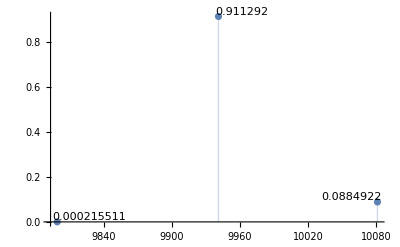

```mathematica
(*Plot instantly since it only contains bins with actual data*)
ListPlot[Labeled[#,#[[2]]]&/@nonZeroData,Filling->Axis,PlotMarkers->None]
```

The result is consistent with the theoretical values

## RNG Extraction histogram Local (./2dbLRW-extrHist.out 70 40.0 0)

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
localData=BinaryReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extractionData\\extraction-Histogram-at-70-50-b40.bin","Integer32"];
Length@localData
```

12220556

```mathematica
localData[[1;;100]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
packedData=Developer`ToPackedArray[localData];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[packedData]
```

True

```mathematica
maxVal=Max[N[packedData]]

(*Fast integer or float counting*)
counts=N[BinCounts[packedData,{0,maxVal+1,1}]]

(*Convert counts to probabilities manually*)
heights=counts/Length[packedData];
```

3.

{0.,0.,68.,1.22205×10^7}

```mathematica
heights
ArrayRules[heights]
```

{0.,0.,5.56439×10^-6,0.999994}

{{3}→5.56439×10^-6,{4}→0.999994,{_}→0}

```mathematica
(*Extract the non-zero data points:{bin_number,probability}*)
nonZeroData=Most[ArrayRules[heights]]/. ({bin_}->prob_)->{bin-1,prob};
```

```mathematica
nonZeroData
Total@nonZeroData[[All,2]]
```

{{2,5.56439×10^-6},{3,0.999994}}

1.

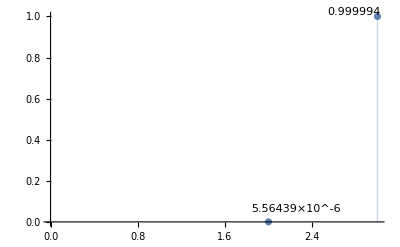

```mathematica
(*Plot instantly since it only contains bins with actual data*)
ListPlot[Labeled[#,#[[2]]]&/@nonZeroData,Filling->Axis,PlotMarkers->None,PlotRange->{{0,3},All}]
```

The result is consistent with the theoretical values

## RNG Extraction histogram From cluster (./2dbLRW-extrHist.out 70 40.0 0) WORK IN PROGESS

It’s so big it crashes Gemini suggested the code below

### crashing

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
rawData=BinaryReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extractionData\\extraction-Histogram-at-70-50-b40-Integer8.bin","Integer8"];
Length@rawData
```

630194176

```mathematica
rawData[[1;;10]]
```

{3,3,3,3,3,3,3,3,3,3}

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
packedData=Developer`ToPackedArray[rawData];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[packedData]
```

True

```mathematica
packedData[[1;;3]]
```

{3,3,3}

```mathematica
maxVal=Max[N[packedData]];

(*Fast integer or float counting*)
counts=N[BinCounts[packedData,{0,maxVal+1,1}]];

(*Convert counts to probabilities manually*)
heights=counts/Length[packedData];
```

```mathematica
heights
ArrayRules[heights]
```

{0.,0.,5.60087×10^-6,0.999994}

{{3}→5.60087×10^-6,{4}→0.999994,{_}→0}

```mathematica
(*Extract the non-zero data points:{bin_number,probability}*)
nonZeroData=Most[ArrayRules[heights]]/. ({bin_}->prob_)->{bin-1,prob};
```

```mathematica
nonZeroData
Total@nonZeroData[[All,2]]
```

{{0,0.5},{38,0.25},{51,0.249999}}

0.999999

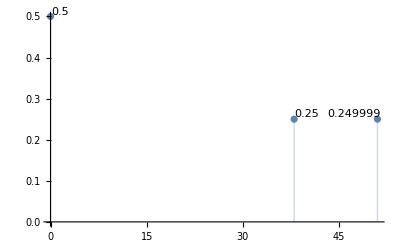

```mathematica
(*Plot instantly since it only contains bins with actual data*)
ListPlot[Labeled[#,#[[2]]]&/@nonZeroData,Filling->Axis,PlotMarkers->None]
```

The result is consistent with the theoretical values

### Gemini

```mathematica
(*1. Initialize a 4-element table to hold counts for 0,1,2,and 3*)tallyCounts={0,0,0,0};

(*2. Open a low-level binary stream to the file*)
stream=OpenRead["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extractionData\\extraction-Histogram-at-70-50-b40-Integer8.bin",BinaryFormat->True];

(*3. Process the file in chunks of 1 million bytes at a time*)
chunkSize=1000000;
```

```mathematica
Internal`WithLocalSettings[None,
While[(chunk=BinaryReadList[stream,"Integer8",chunkSize])=!={},(*Scan through each {val,count} pair from Tally and update tallyCounts*)Scan[Function[pair,With[{val=pair[[1]],count=pair[[2]]},If[0<=val<=3,tallyCounts[[val+1]]+=count]]],Tally[chunk]]],

(*4. ALWAYS close the file stream securely if it finishes or aborts*)Close[stream]
];
```

```mathematica
(*5. Compute the final probabilities from your tiny tally list*)
heights=N[tallyCounts/Total[tallyCounts]];

Print["Final Probabilities: ",heights];
```

Final Probabilities: {0.,4.01468×10^-9,5.68749×10^-6,0.999994}

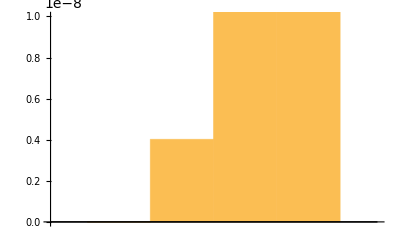

```mathematica
BarChart[heights,BarSpacing->0,PlotRange->{All,{0,10^-8}}]
```

```mathematica
(*yess this is the expected PDF!!*)
```

Rates and normalized probabilities with tot rate 1.90158222785e-119
  Rate to the top neighbor:     7.29784472775e-128       Prob:  3.83777499646e-09
  Rate to the bottom neighbor:  1.08033634696e-124       Prob:  5.68124970425e-06
  Rate to the right neighbor:   8.26607443788e-131       Prob:  4.34694556818e-12
  Rate to the left neighbor:    1.90157141718e-119       Prob:  0.999994314908

```mathematica
(*I didn't run the code long enough to see the e-12*)
```

## L=141 path Lengths histogram

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\b=10.000000-LRW-2d-square-lattice-data-141_repeat-100000.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{71,75}

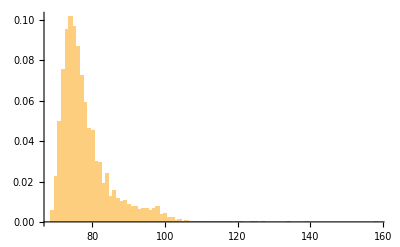

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

### Mean

```mathematica
(Total@pathLenghts)/Length[pathLenghts]//N
```

78.0672

## L=21 path Lengths histograms

```mathematica
lbar={}
h={}
ϵ=1
```

{}

{}

1

### 1e-1 is bad: it crosses itself...

### 1e-2 only crossed itself once in 10^5 runs (1min30s)

```mathematica
ϵ=ϵ+1
```

2

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-2.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,17},{21,13}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{17,13}

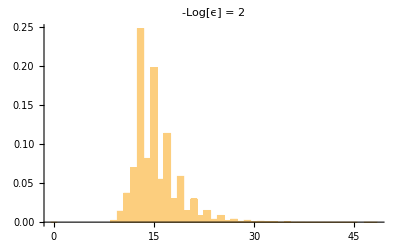

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152}

### 1e-3 (no crosses) (1min56s)

```mathematica
ϵ=ϵ+1
```

3

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-3.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,13},{21,15}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{13,15}

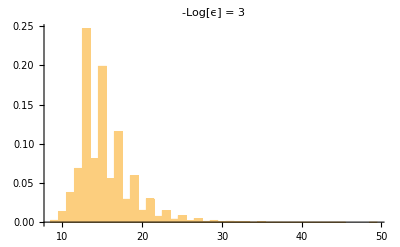
{-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128}

### 1e-4 (2min51s)

```mathematica
ϵ=ϵ+1
```

4

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-4.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,16},{21,20}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{16,20}

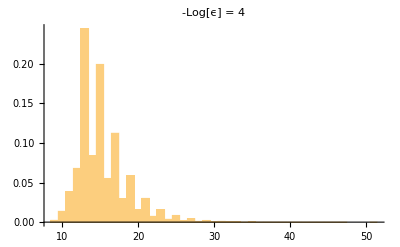
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255}

### 1e-5 (~3min)

```mathematica
ϵ=ϵ+1
```

5

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-5.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

123876

```mathematica
pathWords[[1;;2]]
```

{{21,13},{21,15}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{13,15}

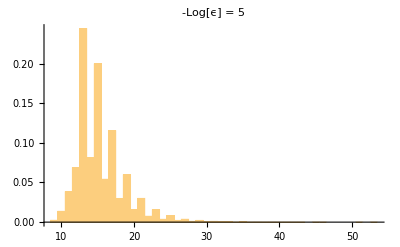
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262}

### 1e-6 (3min4s)

```mathematica
ϵ=ϵ+1
```

6

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-6.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,15},{21,15}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{15,15}

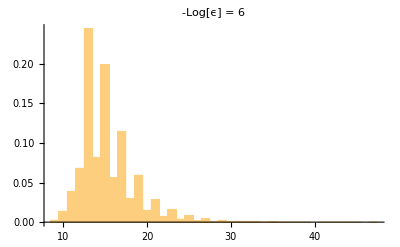
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245}

### 1e-7 (3min36s)

```mathematica
ϵ=ϵ+1
```

7

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-7.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,13},{21,14}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{13,14}

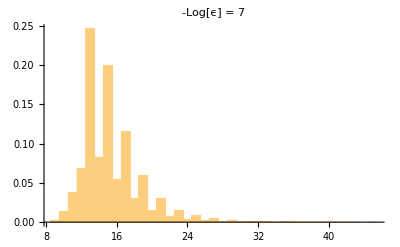
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245,15.3238}

### 1e-8 (4min5s)

```mathematica
ϵ=ϵ+1
```

8

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-8.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,17},{21,10}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{17,10}

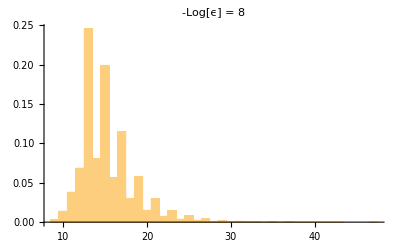
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245,15.3238,15.3112}

### 1e-9 (4min18s)

```mathematica
ϵ=ϵ+1
```

9

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-9.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,16},{21,14}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{16,14}

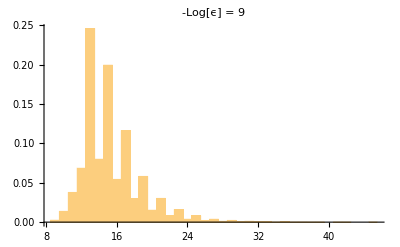
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245,15.3238,15.3112,15.329}

### 1e-10 (4min36s)

```mathematica
ϵ=ϵ+1
```

10

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-10.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100901

```mathematica
pathWords[[1;;2]]
```

{{21,23},{21,23}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{23,23}

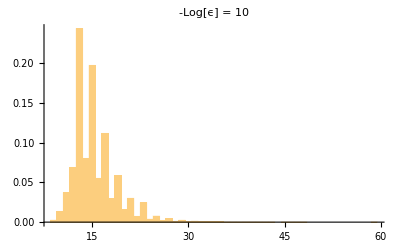
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245,15.3238,15.3112,15.329,15.3984}

### 1e-11 (5min0s)

```mathematica
ϵ=ϵ+1
```

11

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-11.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,14},{21,10}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{14,10}

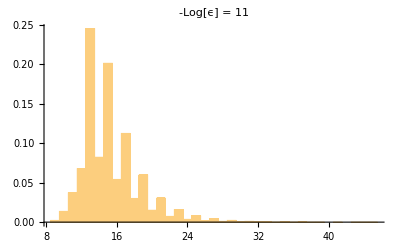
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245,15.3238,15.3112,15.329,15.3984,15.3372}

### 1e-12 (5min6s)

```mathematica
ϵ=ϵ+1
```

12

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-12.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,17},{21,10}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{17,10}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]];
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245,15.3238,15.3112,15.329,15.3984,15.3372,15.3192}

### 1e-13 (5min39s)

```mathematica
ϵ=ϵ+1
```

13

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-13.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,23},{21,13}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{23,13}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]];
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245,15.3238,15.3112,15.329,15.3984,15.3372,15.3192,15.3215}

### 1e-14 (7min41s)

```mathematica
ϵ=ϵ+1
```

14

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-14.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,12},{21,11}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{12,11}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]];
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245,15.3238,15.3112,15.329,15.3984,15.3372,15.3192,15.3215,15.3295}

### 1e-15 (7min17s)

```mathematica
ϵ=ϵ+1
```

15

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d\\b=2_LRW-2d-square-lattice-data-21_repeat-100000_tol-1e-15.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

100000

```mathematica
pathWords[[1;;2]]
```

{{21,17},{21,13}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{17,13}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]];
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{15.3152,15.3128,15.3255,15.3262,15.3245,15.3238,15.3112,15.329,15.3984,15.3372,15.3192,15.3215,15.3295,15.3284}

### Plot of lbar VS exponent

```mathematica
lbarData=Table[{i+1,lbar[[i]]},{i,1,Length@lbar}]
```

{{2,15.3152},{3,15.3128},{4,15.3255},{5,15.3262},{6,15.3245},{7,15.3238},{8,15.3112},{9,15.329},{10,15.3984},{11,15.3372},{12,15.3192},{13,15.3215},{14,15.3295},{15,15.3284}}

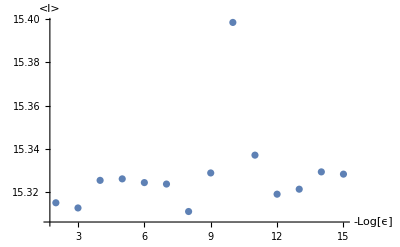

```mathematica
ListPlot[lbarData,AxesLabel->{"-Log[ϵ]","<l>"},PlotRange->All]
```

```mathematica
(*it seems that already at ϵ=1e-4 we get a good result*)
```

### Histograms

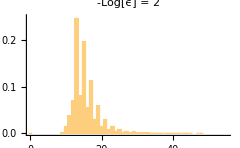
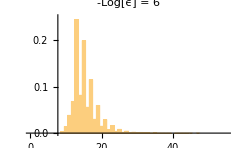
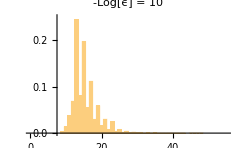
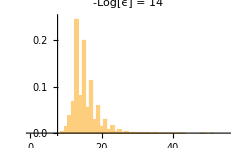
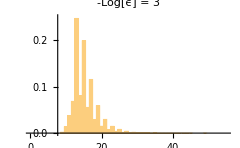
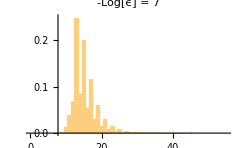
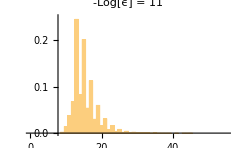
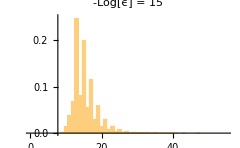
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
(*1. Force every histogram in your list to share the exact same Y-axis scale*)synchronizedHistograms=Map[Show[#,PlotRange->{{0,55},{0,.25}},ImageSize->240]&,h];

(*2. Display them instantly in a clean grid layout (3 columns)*)
Multicolumn[synchronizedHistograms,4,Appearance->"Framed"]
```

### Frequency of the mean

```mathematica
bin15Heights=Map[With[{rects=SelectFirst[Cases[#,_Rectangle,All],#[[1,1]]<=15.0<=#[[2,1]]&]},rects[[2,2]]]&,h]
```

{0.197638,0.19909,0.19922,0.199417,0.19879,0.19935,0.19899,0.19942,0.197382,0.20139,0.19948,0.20006,0.20008,0.19982}

```mathematica
bin15Heightsdata=Table[{i+1,bin15Heights[[i]]},{i,1,Length@lbar}]
```

{{2,0.197638},{3,0.19909},{4,0.19922},{5,0.199417},{6,0.19879},{7,0.19935},{8,0.19899},{9,0.19942},{10,0.197382},{11,0.20139},{12,0.19948},{13,0.20006},{14,0.20008},{15,0.19982}}

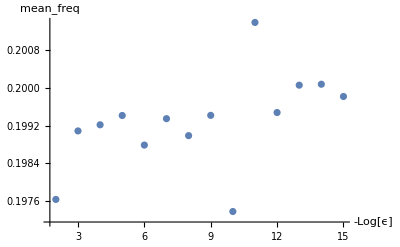

```mathematica
ListPlot[bin15Heightsdata,AxesLabel->{"-Log[ϵ]","mean_freq"},PlotRange->All]
```

### Frequency of the mode

```mathematica
(*1. Find all rectangles inside the graphic object*)allRectangles=Cases[h[[1]],_Rectangle,All];

(*2. Find the rectangle with the maximum Y-max (highest bar)*)
tallestRectangle=MaximalBy[allRectangles,#[[2,2]]&][[1]];

(*3. Extract its X boundaries to identify the bin value*)
modeBin={tallestRectangle[[{1,2},1]]/.Rectangle->Sequence}

mode=Mean@modeBin
```

{12.5,13.5}

13.

```mathematica
modesHistory=Map[With[{tallest=MaximalBy[Cases[#,_Rectangle,All],#[[2,2]]&][[1]]},(*Calculate the floor/midpoint of the tallest bin to get the value*)Ceiling[tallest[[1,1]]]]&,h]
```

{13,13,13,13,13,13,13,13,13,13,13,13,13,13}

```mathematica
(*The mode does not change*)
```

```mathematica
binModeHeights=Map[With[{rects=SelectFirst[Cases[#,_Rectangle,All],#[[1,1]]<=13.0<=#[[2,1]]&]},rects[[2,2]]]&,h]
```

{0.247658,0.24711,0.24441,0.244059,0.24456,0.24648,0.24576,0.2457,0.243893,0.24516,0.24664,0.2463,0.24562,0.2464}

```mathematica
binModeHeightsdata=Table[{i+1,binModeHeights[[i]]},{i,1,Length@binModeHeights}]
```

{{2,0.247658},{3,0.24711},{4,0.24441},{5,0.244059},{6,0.24456},{7,0.24648},{8,0.24576},{9,0.2457},{10,0.243893},{11,0.24516},{12,0.24664},{13,0.2463},{14,0.24562},{15,0.2464}}

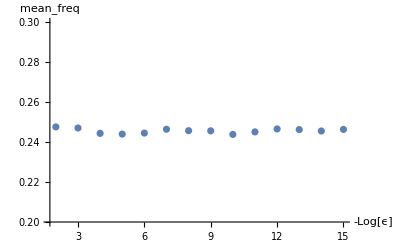

```mathematica
ListPlot[binModeHeightsdata,AxesLabel->{"-Log[ϵ]","mean_freq"},PlotRange->{All,{0.2,0.3}}]
```

### Observable: Σ_l (|f(l)-g(l)|)/(f(l)+g(l))

```mathematica
(*1. Find all rectangles that exist*)
rectangles=Cases[h[[1]],_Rectangle,All];

(*2. Find the full absolute limits of the X-axis from the plot geometry*)
xMin=0.;
xMax=55.;

(*3. Reconstruct your full step-by-step bin sequence (assuming bin width=1)*)
allBinMidpoints=Range[xMin+0.5,xMax-0.5,1.];
```

```mathematica
(*4. Build a lookup association from the rectangles that DO exist*)
existingHeights=Association[Map[(#[[1,1]]+1)->#[[2,2]]&,rectangles]];

(*5. Map across all possible bins,filling in 0. if the bin was empty*)
fullHistogramData=Table[{midpoint,Lookup[existingHeights,midpoint,0.]},{midpoint,allBinMidpoints}];
```

```mathematica
With[{rects=Cases[#,_Rectangle,All]},Table[{midpoint,Lookup[Association[Map[(#[[1,1]]+1)->#[[2,2]]&,rects]],midpoint,0.]},{midpoint,allBinMidpoints}]]&@h[[5]]
```

{{0.5,0.},{1.5,0.},{2.5,0.},{3.5,0.},{4.5,0.},{5.5,0.},{6.5,0.},{7.5,0.},{8.5,0.},{9.5,0.00255},{10.5,0.01376},{11.5,0.0383},{12.5,0.06812},{13.5,0.24456},{14.5,0.0818},{15.5,0.19879},{16.5,0.05588},{17.5,0.11476},{18.5,0.02989},{19.5,0.05945},{20.5,0.01499},{21.5,0.02848},{22.5,0.00729},{23.5,0.01609},{24.5,0.00396},{25.5,0.00809},{26.5,0.00204},{27.5,0.00451},{28.5,0.00103},{29.5,0.00218},{30.5,0.00058},{31.5,0.00123},{32.5,0.00033},{33.5,0.00042},{34.5,0.00008},{35.5,0.00032},{36.5,0.00013},{37.5,0.00015},{38.5,0.00004},{39.5,0.00009},{40.5,0.},{41.5,0.00004},{42.5,0.00002},{43.5,0.00002},{44.5,0.00001},{45.5,0.00001},{46.5,0.},{47.5,0.00001},{48.5,0.},{49.5,0.},{50.5,0.},{51.5,0.},{52.5,0.},{53.5,0.},{54.5,0.}}

```mathematica
Length[h]
```

14

```mathematica
allBins=Map[With[{rects=Cases[#,_Rectangle,All]},Table[{midpoint,Lookup[Association[Map[(#[[1,1]]+1)->#[[2,2]]&,rects]],midpoint,0.]},{midpoint,allBinMidpoints}]]&,h];
```

```mathematica
allBins[[All,13]]
allBins[[All,13,2]]
allBins[[All,13,2]][[1;;2]]
```

{{12.5,0.0694593},{12.5,0.06854},{12.5,0.06797},{12.5,0.0686977},{12.5,0.06812},{12.5,0.06783},{12.5,0.06873},{12.5,0.0686},{12.5,0.0687803},{12.5,0.06781},{12.5,0.06931},{12.5,0.06734},{12.5,0.06842},{12.5,0.06815}}

{0.0694593,0.06854,0.06797,0.0686977,0.06812,0.06783,0.06873,0.0686,0.0687803,0.06781,0.06931,0.06734,0.06842,0.06815}

{0.0694593,0.06854}

```mathematica
Table[
Sum[
With[{f=allBins[[All,i,2]][[j]],g=allBins[[All,i,2]][[j+1]]},
Limit[Abs[f-g]/(f+x),x->g]]
,{i,1,Length[allBins[[1]]]}]
,{j,1,Length[allBins]-1}]
```

{6.57654,5.91571,4.98342,8.03048,5.39476,5.27536,6.41686,6.80437,8.85556,7.32837,6.78181,8.11175,7.63166}

## L=101 path Lengths histograms (From Cluster)

```mathematica
lbar={}
h={}
ϵ=1
```

{}

{}

1

### 1e-2

```mathematica
ϵ=ϵ+1
```

2

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-2.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

1000000

```mathematica
pathWords[[1;;2]]
```

{{101,90},{101,79}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{90,79}

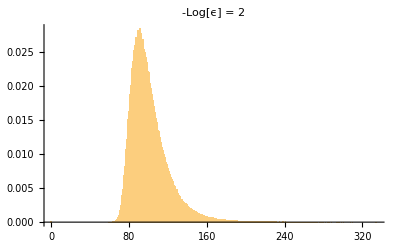

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047}

### 1e-3

```mathematica
ϵ=ϵ+1
```

3

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-3.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

1000000

```mathematica
pathWords[[1;;2]]
```

{{101,97},{101,92}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{97,92}

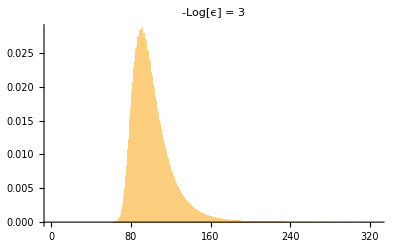
{-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793}

### 1e-4

```mathematica
ϵ=ϵ+1
```

4

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-4.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

1000000

```mathematica
pathWords[[1;;2]]
```

{{101,84},{101,79}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{84,79}

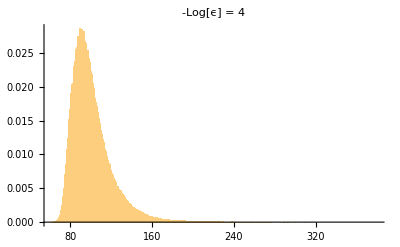
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781}

### 1e-5

```mathematica
ϵ=ϵ+1
```

5

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-5.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

1000000

```mathematica
pathWords[[1;;2]]
```

{{101,89},{101,85}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{89,85}

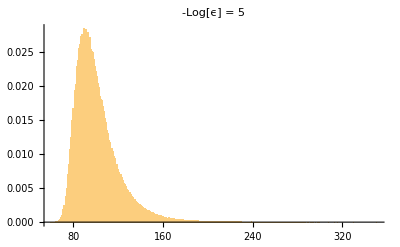
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802}

### 1e-6

```mathematica
ϵ=ϵ+1
```

6

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-6.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

1000000

```mathematica
pathWords[[1;;2]]
```

{{101,85},{101,95}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{85,95}

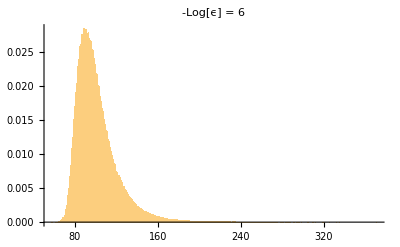
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802,100.797}

### 1e-7

```mathematica
ϵ=ϵ+1
```

7

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-7.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

1000000

```mathematica
pathWords[[1;;2]]
```

{{101,93},{101,80}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{93,80}

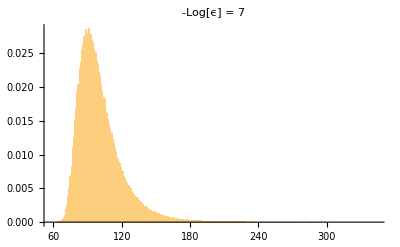
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802,100.797,100.783}

### 1e-8

```mathematica
ϵ=ϵ+1
```

8

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-8.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

1000000

```mathematica
pathWords[[1;;2]]
```

{{101,77},{101,103}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{77,103}

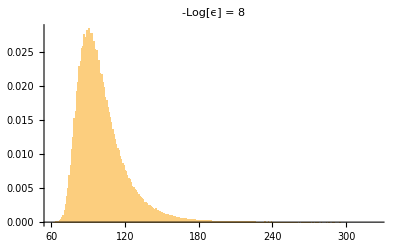
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802,100.797,100.783,100.799}

### 1e-9

```mathematica
ϵ=ϵ+1
```

9

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-9.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

928688

```mathematica
pathWords[[1;;2]]
```

{{101,93},{101,84}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{93,84}

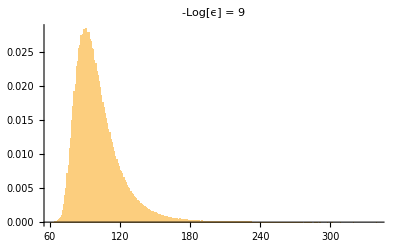
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802,100.797,100.783,100.799,100.78}

### 1e-10

```mathematica
ϵ=ϵ+1
```

10

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-10.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

818933

```mathematica
pathWords[[1;;2]]
```

{{101,115},{101,97}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{115,97}

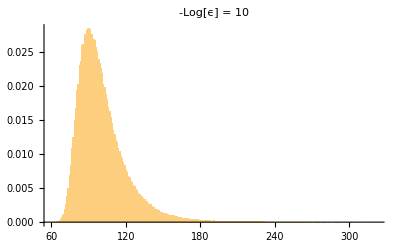
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802,100.797,100.783,100.799,100.78,100.777}

### 1e-11

```mathematica
ϵ=ϵ+1
```

11

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-11.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

731848

```mathematica
pathWords[[1;;2]]
```

{{101,97},{101,121}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{97,121}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]]
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802,100.797,100.783,100.799,100.78,100.777,100.748}

### 1e-12

```mathematica
ϵ=ϵ+1
```

12

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-12.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

659591

```mathematica
pathWords[[1;;2]]
```

{{101,106},{101,76}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{106,76}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]];
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802,100.797,100.783,100.799,100.78,100.777,100.748,100.803}

### 1e-13

```mathematica
ϵ=ϵ+1
```

13

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-13.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

600840

```mathematica
pathWords[[1;;2]]
```

{{101,84},{101,77}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{84,77}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]];
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802,100.797,100.783,100.799,100.78,100.777,100.748,100.803,100.793}

### 1e-14

```mathematica
ϵ=ϵ+1
```

14

```mathematica
(*rawData=Flatten@(ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\extraction-Histogram.dat"}],"CSV"]); *)
(* MODIFY FILE NAME *)
pathWords=ReadList["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\2d-FromCluster\\DifferentPrecisionAnalysis\\b=2_LRW-2d-square-lattice-data-101_repeat-1000000_tol-1e-14.csv",Word,RecordLists->True,WordSeparators->{","," ","\t"}];
Length@pathWords
```

575360

```mathematica
pathWords[[1;;2]]
```

{{101,136},{101,90}}

```mathematica
pathLenghts=ToExpression[pathWords[[All,2;;]]];
```

```mathematica
(*Force the data into a flat,contiguous machine-number array*)
pathLenghts=Developer`ToPackedArray[Flatten[pathLenghts]];

(*Verify it worked (should return True)*)
Developer`PackedArrayQ[pathLenghts]
```

True

```mathematica
pathLenghts[[1;;2]]
```

{136,90}

```mathematica
AppendTo[h,Histogram[pathLenghts,{1},"Probability",PlotRange->All,PlotLabel->Row[{"-Log[ϵ] = ",ϵ}]]];
Histogram[pathLenghts,{1},"PDF",PlotRange->{All,All}];
```

#### Mean

```mathematica
AppendTo[lbar,(Total@pathLenghts)/Length[pathLenghts]//N]
```

{101.047,100.793,100.781,100.802,100.797,100.783,100.799,100.78,100.777,100.748,100.803,100.793,100.791}

### Plot of lbar VS exponent

```mathematica
lbarData=Table[{i+1,lbar[[i]]},{i,1,Length@lbar}]
```

{{2,101.047},{3,100.793},{4,100.781},{5,100.802},{6,100.797},{7,100.783},{8,100.799},{9,100.78},{10,100.777},{11,100.748},{12,100.803},{13,100.793},{14,100.791}}

```mathematica
ListPlot[lbarData,AxesLabel->{"-Log[ϵ]","<l>"},PlotRange->All]
```

-Graphics-

```mathematica
(*it seems that already at ϵ=1e-4 we get a good result*)
```

### Histograms

```mathematica
(*1. Force every histogram in your list to share the exact same Y-axis scale*)synchronizedHistograms=Map[Show[#,PlotRange->{{50,400},{0,0.0001}},ImageSize->220]&,h];

(*2. Display them instantly in a clean grid layout (3 columns)*)
Multicolumn[synchronizedHistograms,4,Appearance->"Framed"]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

### Frequency of the mean

```mathematica
meanHistory=Table[With[{mean=Select[Cases[#,_Rectangle,All],#[[1,1]]<=lbar[[i]]<=#[[2,1]]&]},(*Calculate the Ceiling of the tallest bin to get the value*)mean[[1,2,2]]]&@h[[i]],
{i,1,Length[h]}];
```

```mathematica
meanHistoryData=Table[{i+1,meanHistory[[i]]},{i,1,Length@lbar}]
```

{{2,0.0219139},{3,0.0215189},{4,0.021767},{5,0.021459},{6,0.021647},{7,0.021714},{8,0.021682},{9,0.0214959},{10,0.0218528},{11,0.0218707},{12,0.0217301},{13,0.0215282},{14,0.0218698}}

```mathematica
ListPlot[meanHistoryData,AxesLabel->{"-Log[ϵ]","mean_freq"},PlotRange->{All,{0.02,0.023}}]
```

-Graphics-

### Frequency of the mode

```mathematica
(*1. Find all rectangles inside the graphic object*)allRectangles=Cases[h[[1]],_Rectangle,All];

(*2. Find the rectangle with the maximum Y-max (highest bar)*)
tallestRectangle=MaximalBy[allRectangles,#[[2,2]]&][[1]];

(*3. Extract its X boundaries to identify the bin value*)
modeBin={tallestRectangle[[{1,2},1]]/.Rectangle->Sequence}

mode=Mean@modeBin
```

{90.5,91.5}

91.

```mathematica
modesHistory=Map[With[{tallest=MaximalBy[Cases[#,_Rectangle,All],#[[2,2]]&][[1]]},(*Calculate the floor/midpoint of the tallest bin to get the value*)Ceiling[tallest[[1,1]]]]&,h]
```

{91,91,89,89,89,91,91,91,90,89,89,91,89}

```mathematica
(*The mode does not change*)
```

```mathematica
binModeHeights=Table[With[{rects=SelectFirst[Cases[#,_Rectangle,All],#[[1,1]]<=modesHistory[[i]]<=#[[2,1]]&]},rects[[2,2]]]&@h[[i]],
{i,1,Length[h]}]
```

{0.0283889,0.0286118,0.028572,0.028438,0.028449,0.02868,0.028507,0.0284412,0.0283967,0.0287396,0.0282796,0.0282821,0.0288324}

```mathematica
binModeHeightsdata=Table[{i+1,binModeHeights[[i]]},{i,1,Length@binModeHeights}]
```

{{2,0.0283889},{3,0.0286118},{4,0.028572},{5,0.028438},{6,0.028449},{7,0.02868},{8,0.028507},{9,0.0284412},{10,0.0283967},{11,0.0287396},{12,0.0282796},{13,0.0282821},{14,0.0288324}}

```mathematica
ListPlot[binModeHeightsdata,AxesLabel->{"-Log[ϵ]","mean_freq"},PlotRange->{All,{0.025,0.031}}]
```

-Graphics-

### Observable: Σ_l (|f(l)-g(l)|)/(f(l)+g(l))

```mathematica
(*1. Find all rectangles that exist*)
rectangles=Cases[h[[1]],_Rectangle,All];

(*2. Find the full absolute limits of the X-axis from the plot geometry*)
xMin=0.;
xMax=450.;

(*3. Reconstruct your full step-by-step bin sequence (assuming bin width=1)*)
allBinMidpoints=Range[xMin+0.5,xMax-0.5,1.];
```

```mathematica
(*4. Build a lookup association from the rectangles that DO exist*)
existingHeights=Association[Map[(#[[1,1]]+1)->#[[2,2]]&,rectangles]];

(*5. Map across all possible bins,filling in 0. if the bin was empty*)
fullHistogramData=Table[{midpoint,Lookup[existingHeights,midpoint,0.]},{midpoint,allBinMidpoints}];
```

```mathematica
With[{rects=Cases[#,_Rectangle,All]},Table[{midpoint,Lookup[Association[Map[(#[[1,1]]+1)->#[[2,2]]&,rects]],midpoint,0.]},{midpoint,allBinMidpoints}]]&@h[[5]]
```

{{0.5,0.},{1.5,0.},{2.5,0.},{3.5,0.},{4.5,0.},{5.5,0.},{6.5,0.},{7.5,0.},{8.5,0.},{9.5,0.},{10.5,0.},{11.5,0.},{12.5,0.},{13.5,0.},{14.5,0.},{15.5,0.},{16.5,0.},{17.5,0.},{18.5,0.},{19.5,0.},{20.5,0.},{21.5,0.},{22.5,0.},{23.5,0.},{24.5,0.},{25.5,0.},{26.5,0.},{27.5,0.},{28.5,0.},{29.5,0.},{30.5,0.},{31.5,0.},{32.5,0.},{33.5,0.},{34.5,0.},{35.5,0.},{36.5,0.},{37.5,0.},{38.5,0.},{39.5,0.},{40.5,0.},{41.5,0.},{42.5,0.},{43.5,0.},{44.5,0.},{45.5,0.},{46.5,0.},{47.5,0.},{48.5,0.},{49.5,0.},{50.5,0.},{51.5,0.},{52.5,0.},{53.5,0.},{54.5,0.},{55.5,0.},{56.5,0.},{57.5,1.×10^-6},{58.5,1.×10^-6},{59.5,0.},{60.5,0.},{61.5,1.×10^-6},{62.5,6.×10^-6},{63.5,0.000018},{64.5,0.000018},{65.5,0.00006},{66.5,0.000103},{67.5,0.000217},{68.5,0.000335},{69.5,0.000689},{70.5,0.001014},{71.5,0.001785},{72.5,0.002405},{73.5,0.003928},{74.5,0.004921},{75.5,0.00678},{76.5,0.008366},{77.5,0.010854},{78.5,0.012482},{79.5,0.015053},{80.5,0.016939},{81.5,0.019107},{82.5,0.020309},{83.5,0.022917},{84.5,0.023934},{85.5,0.025745},{86.5,0.026129},{87.5,0.027621},{88.5,0.027345},{89.5,0.028449},{90.5,0.027914},{91.5,0.028356},{92.5,0.027549},{93.5,0.027799},{94.5,0.02695},{95.5,0.026633},{96.5,0.025333},{97.5,0.025164},{98.5,0.024036},{99.5,0.023226},{100.5,0.021899},{101.5,0.021647},{102.5,0.020104},{103.5,0.019894},{104.5,0.018412},{105.5,0.01768},{106.5,0.016706},{107.5,0.016214},{108.5,0.015096},{109.5,0.014385},{110.5,0.013469},{111.5,0.013318},{112.5,0.012143},{113.5,0.01185},{114.5,0.010952},{115.5,0.010356},{116.5,0.009765},{117.5,0.009203},{118.5,0.008652},{119.5,0.008409},{120.5,0.0075},{121.5,0.007248},{122.5,0.006908},{123.5,0.00653},{124.5,0.006161},{125.5,0.005763},{126.5,0.005222},{127.5,0.005204},{128.5,0.004776},{129.5,0.004629},{130.5,0.004306},{131.5,0.004088},{132.5,0.003829},{133.5,0.003656},{134.5,0.003404},{135.5,0.003268},{136.5,0.002978},{137.5,0.00291},{138.5,0.002684},{139.5,0.002632},{140.5,0.00237},{141.5,0.002269},{142.5,0.002125},{143.5,0.002054},{144.5,0.001948},{145.5,0.001866},{146.5,0.001683},{147.5,0.001628},{148.5,0.001566},{149.5,0.001426},{150.5,0.001371},{151.5,0.001324},{152.5,0.001249},{153.5,0.001123},{154.5,0.001083},{155.5,0.001062},{156.5,0.001043},{157.5,0.000948},{158.5,0.00085},{159.5,0.000897},{160.5,0.000796},{161.5,0.000794},{162.5,0.00072},{163.5,0.000698},{164.5,0.000633},{165.5,0.00061},{166.5,0.000589},{167.5,0.000567},{168.5,0.00053},{169.5,0.000506},{170.5,0.000459},{171.5,0.000461},{172.5,0.000438},{173.5,0.000407},{174.5,0.000393},{175.5,0.000348},{176.5,0.000327},{177.5,0.000325},{178.5,0.000349},{179.5,0.000306},{180.5,0.000267},{181.5,0.000277},{182.5,0.000259},{183.5,0.000251},{184.5,0.000213},{185.5,0.000223},{186.5,0.000213},{187.5,0.000169},{188.5,0.000177},{189.5,0.00016},{190.5,0.000173},{191.5,0.000166},{192.5,0.000131},{193.5,0.000147},{194.5,0.000148},{195.5,0.000103},{196.5,0.000108},{197.5,0.000116},{198.5,0.000098},{199.5,0.000106},{200.5,0.000107},{201.5,0.000077},{202.5,0.000109},{203.5,0.000082},{204.5,0.000088},{205.5,0.000076},{206.5,0.000083},{207.5,0.000084},{208.5,0.000088},{209.5,0.000057},{210.5,0.000057},{211.5,0.000055},{212.5,0.000052},{213.5,0.000056},{214.5,0.000047},{215.5,0.000047},{216.5,0.000047},{217.5,0.000029},{218.5,0.000042},{219.5,0.000033},{220.5,0.000034},{221.5,0.000021},{222.5,0.000038},{223.5,0.000024},{224.5,0.000034},{225.5,0.000035},{226.5,0.000025},{227.5,0.000028},{228.5,0.000024},{229.5,0.000024},{230.5,0.000021},{231.5,0.00002},{232.5,0.000023},{233.5,0.000016},{234.5,0.000022},{235.5,0.000013},{236.5,0.000018},{237.5,0.000015},{238.5,0.000011},{239.5,9.×10^-6},{240.5,0.000019},{241.5,9.×10^-6},{242.5,9.×10^-6},{243.5,7.×10^-6},{244.5,6.×10^-6},{245.5,0.000012},{246.5,6.×10^-6},{247.5,8.×10^-6},{248.5,0.000011},{249.5,0.00001},{250.5,6.×10^-6},{251.5,5.×10^-6},{252.5,5.×10^-6},{253.5,9.×10^-6},{254.5,3.×10^-6},{255.5,1.×10^-6},{256.5,5.×10^-6},{257.5,6.×10^-6},{258.5,5.×10^-6},{259.5,6.×10^-6},{260.5,0.000014},{261.5,3.×10^-6},{262.5,4.×10^-6},{263.5,4.×10^-6},{264.5,2.×10^-6},{265.5,5.×10^-6},{266.5,4.×10^-6},{267.5,1.×10^-6},{268.5,4.×10^-6},{269.5,1.×10^-6},{270.5,0.},{271.5,4.×10^-6},{272.5,3.×10^-6},{273.5,3.×10^-6},{274.5,2.×10^-6},{275.5,1.×10^-6},{276.5,0.},{277.5,0.},{278.5,1.×10^-6},{279.5,1.×10^-6},{280.5,1.×10^-6},{281.5,4.×10^-6},{282.5,0.},{283.5,2.×10^-6},{284.5,3.×10^-6},{285.5,2.×10^-6},{286.5,2.×10^-6},{287.5,1.×10^-6},{288.5,2.×10^-6},{289.5,0.},{290.5,0.},{291.5,1.×10^-6},{292.5,1.×10^-6},{293.5,0.},{294.5,2.×10^-6},{295.5,0.},{296.5,2.×10^-6},{297.5,0.},{298.5,1.×10^-6},{299.5,0.},{300.5,0.},{301.5,0.},{302.5,0.},{303.5,0.},{304.5,1.×10^-6},{305.5,1.×10^-6},{306.5,0.},{307.5,0.},{308.5,0.},{309.5,1.×10^-6},{310.5,1.×10^-6},{311.5,0.},{312.5,1.×10^-6},{313.5,0.},{314.5,0.},{315.5,0.},{316.5,0.},{317.5,0.},{318.5,0.},{319.5,1.×10^-6},{320.5,2.×10^-6},{321.5,0.},{322.5,0.},{323.5,0.},{324.5,0.},{325.5,1.×10^-6},{326.5,0.},{327.5,0.},{328.5,0.},{329.5,0.},{330.5,0.},{331.5,0.},{332.5,1.×10^-6},{333.5,0.},{334.5,0.},{335.5,1.×10^-6},{336.5,0.},{337.5,0.},{338.5,0.},{339.5,0.},{340.5,0.},{341.5,0.},{342.5,0.},{343.5,0.},{344.5,0.},{345.5,0.},{346.5,0.},{347.5,0.},{348.5,0.},{349.5,0.},{350.5,0.},{351.5,0.},{352.5,0.},{353.5,0.},{354.5,0.},{355.5,0.},{356.5,0.},{357.5,0.},{358.5,0.},{359.5,0.},{360.5,0.},{361.5,0.},{362.5,0.},{363.5,0.},{364.5,0.},{365.5,0.},{366.5,0.},{367.5,0.},{368.5,0.},{369.5,0.},{370.5,0.},{371.5,1.×10^-6},{372.5,0.},{373.5,0.},{374.5,0.},{375.5,0.},{376.5,0.},{377.5,0.},{378.5,0.},{379.5,0.},{380.5,0.},{381.5,0.},{382.5,0.},{383.5,0.},{384.5,0.},{385.5,0.},{386.5,0.},{387.5,0.},{388.5,0.},{389.5,0.},{390.5,0.},{391.5,0.},{392.5,0.},{393.5,0.},{394.5,0.},{395.5,0.},{396.5,0.},{397.5,0.},{398.5,0.},{399.5,0.},{400.5,0.},{401.5,0.},{402.5,0.},{403.5,0.},{404.5,0.},{405.5,0.},{406.5,0.},{407.5,0.},{408.5,0.},{409.5,0.},{410.5,0.},{411.5,0.},{412.5,0.},{413.5,0.},{414.5,0.},{415.5,0.},{416.5,0.},{417.5,0.},{418.5,0.},{419.5,0.},{420.5,0.},{421.5,0.},{422.5,0.},{423.5,0.},{424.5,0.},{425.5,0.},{426.5,0.},{427.5,0.},{428.5,0.},{429.5,0.},{430.5,0.},{431.5,0.},{432.5,0.},{433.5,0.},{434.5,0.},{435.5,0.},{436.5,0.},{437.5,0.},{438.5,0.},{439.5,0.},{440.5,0.},{441.5,0.},{442.5,0.},{443.5,0.},{444.5,0.},{445.5,0.},{446.5,0.},{447.5,0.},{448.5,0.},{449.5,0.}}

```mathematica
Length[h]
```

13

```mathematica
allBins=Map[With[{rects=Cases[#,_Rectangle,All]},Table[{midpoint,Lookup[Association[Map[(#[[1,1]]+1)->#[[2,2]]&,rects]],midpoint,0.]},{midpoint,allBinMidpoints}]]&,h];
```

```mathematica
allBins[[All,13]]
allBins[[All,13,2]]
allBins[[All,13,2]][[1;;2]]
```

{{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.},{12.5,0.}}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.}

```mathematica
obs=Table[
Sum[
With[{f=allBins[[All,i,2]][[j]],g=allBins[[All,i,2]][[j+1]]},
Limit[Abs[f-g]/(f+x),x->g]]
,{i,1,Length[allBins[[1]]]}]
,{j,1,Length[allBins]-1}]
```

{49.5455,47.9385,36.562,50.6311,45.2038,36.2135,36.8239,37.2193,46.4416,46.1479,52.2329,40.6095}

```mathematica
obsData=Table[{i+1,#[[i]]},{i,1,Length@#}]&@obs
```

{{2,49.5455},{3,47.9385},{4,36.562},{5,50.6311},{6,45.2038},{7,36.2135},{8,36.8239},{9,37.2193},{10,46.4416},{11,46.1479},{12,52.2329},{13,40.6095}}

```mathematica
ListPlot[obsData,AxesLabel->{"-Log[ϵ]","mean_freq"},PlotRange->{All,{30,60}}]
```

-Graphics-

# Nice path Lengths analysis (MOST OF THE FILES ARE IN A ZIP)

```mathematica
Quit[]
```

## Function definitions

```mathematica
ParallelMap[Plus,{1,2}]
```

{1,2}

```mathematica
ClearAll[Rotate90,ReflectX,GetSymmetryFamily];

(*Rotates 90° counter-clockwise around the first point of the path*)Rotate90[path_List]:=With[{center=path[[1]]},Map[({-(#[[2]]-center[[2]])+center[[1]],(#[[1]]-center[[1]])+center[[2]]})&,path]]

(*Reflects horizontally across the vertical line passing through the first point (x->-x)*)
ReflectX[path_List]:=With[{center=path[[1]]},Map[({-(#[[1]]-center[[1]])+center[[1]],#[[2]]})&,path]]

(*Generates all 8 unique rotation and reflection variants of a path*)GetSymmetryFamily[path_List]:=With[{rotations=NestList[Rotate90,path,3]},
Join[rotations,Map[ReflectX,rotations]]]
```

```mathematica
ClearAll[AnalyzeSymmetricPaths]

(*Comparison test:Returns True if path2 is a valid symmetry transformation of path1*)AreSymmetricQ[path1_List,path2_List]:=MemberQ[GetSymmetryFamily[path1],path2];

(*The master function to process your paths array*)
AnalyzeSymmetricPaths[allPaths_List]:=Module[{grouped,tally},(*Group identical paths under rotation/reflection*)grouped=Gather[allPaths,AreSymmetricQ];
(*Return a structured dataset:{Unique Representative Path,Family Occurrence Count}*)tally=Table[{First[g],Length[g]},{g,grouped}];

Reverse[SortBy[tally,Last]]
];
```

```mathematica
MergeTwoTallies[tally1_List,tally2_List]:=Module[{combined=tally1,matched,path2,count2},
Do[(*Extract components explicitly using Pattern Matching*)
path2=item[[1]];
count2=item[[2]];
(*Your existing logic*)
matched=Position[combined,_?(AreSymmetricQ[#[[1]],path2]&),{1},1]//Quiet;

If[Length[matched]>0,
combined[[matched[[1,1]],2]]+=count2,
AppendTo[combined,{path2,count2}]
],

{item,tally2} (*Loops through each full pair in tally2*)];

combined
];
```

```mathematica
IterativeSymmetricTally[allPaths_List,batchSize_Integer:100]:=Module[{batches,currentTallies},
DistributeDefinitions[AnalyzeSymmetricPaths,MergeTwoTallies,AreSymmetricQ];
(*1. Initial Step: partition and analyze individual batches*)
batches=Partition[allPaths,UpTo[batchSize]];
currentTallies=ParallelMap[AnalyzeSymmetricPaths,batches];

(*2. Reduction Loop: merge pairs of batches until only 1 master tally is left*)
While[Length[currentTallies]>1,

currentTallies=If[OddQ[Length[currentTallies]],

(*If odd number of batches,hold the last one and merge the pairs*)Append[Map[Apply[MergeTwoTallies],Partition[Drop[currentTallies,-1],2]],Last[currentTallies]],

(*If even,merge all pairs straight across*)
Map[Apply[MergeTwoTallies],Partition[currentTallies,2]]
];
Print["Remaining batch blocks to merge: ",Length[currentTallies]];
];
(*3. Final Sort by count in descending order*)
Reverse[SortBy[First[currentTallies],Last]]
];
```

# b=1

## L=5 (active is 3) path Lengths histograms (b-1LRW-n5.csv )

```mathematica
n=3;

(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n5.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

11030

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{2,2},{2,1}},2791}

{{{2,2},{2,3}},2799}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities,
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

```mathematica
(*In accordance with the expected homogeneus 1/4*)
```

## L=5 (active is 3) path Lengths histograms (b-1LRW-n5-UpdatedStopCond.csv)

### All paths

```mathematica
n=3;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n5-UpdatedStopCond.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

40000

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}];
```

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{2,2},{1,2}},10017}

{{{2,2},{3,2}},10150}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities,
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

## L=5 (active is 3) path Lengths histograms (b-1LRW-n5-NoReordering.csv )

### All paths

```mathematica
n=3;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n5-NoReordering.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

80000

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}];
```

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{2,2},{1,2}},19754}

{{{2,2},{2,3}},20316}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities,
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

## L=5 (active is 3) path Lengths histograms (b-1LRW-n5-NoReordering-Double.csv )

### All paths

```mathematica
n=3;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n5-NoReordering-Double.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

80000

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}];
```

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{2,2},{3,2}},19806}

{{{2,2},{2,3}},20185}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities,
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

```mathematica
Histogram[Table[RandomInteger[3],40000]]
```

-Graphics-

## L=7 (active is 5) path Lengths histograms (b-1LRW-n7.csv )

```mathematica
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n7.csv","Text"],"\n\n"|"\r\n\r\n"]];
```

```mathematica
rawBlocks[[{1}]]
```

{		3,		3,		  ,		
		2,		3,		3,		3
		2,		2,		2,		3
		1,		2,		2,		2}

```mathematica
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=Map[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]]
```

{{3,3},{4,3},{4,2},{3,2},{2,2},{1,2}}

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
(*Output format:{{path1,count1},{path2,count2},...}*)
```

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97,"ColorFunction"][#2[[1]]],Line[#1]}&,pathCounts[[1;;-1,1]]]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}]
```

-Graphics-

```mathematica
pathCounts[[All,1]]
```

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Apply the function across all paths to get a list of numbers*)
lengthsList=Map[Length,paths];

(*Plot the distribution of the resulting lengths*)
Histogram[lengthsList,Automatic,"Probability",Frame->True,ChartStyle->RGBColor[0.87, 0.71, 0.34],FrameLabel->{"Path Length","Relative Probability"},ImageSize->450]
```

-Graphics-

```mathematica
(*3. Extract just the counts for your histogram*)
countsOnly=pathCounts[[All,2]];

(*4. Plot the histogram of path frequencies*)
Histogram[countsOnly,{1},"Probability",Frame->True,FrameLabel->{"Number of Occurrences","Number of Unique Paths"},PlotLabel->"Path Duplication Distribution",ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->400]
```

-Graphics-

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

(*3. Generate the BarChart with values on top and paths on the bottom*)
BarChart[probabilities,ChartLabels->Placed[pathLabels,Axis,Rotate[#,45Degree]&],(*Rotates labels so they don't overlap*)ChartLabels->Placed[Around[#,0]&/@probabilities,Above],(*Forces values on top of bars*)LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Unique Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",ChartStyle->RGBColor[0.87,0.71,0.34],ImageSize->900,(*Made wider to accommodate labels nicely*)PlotRange->{All,{0,Max[probabilities]*1.15}} (*Leaves room at the top for the numbers*)]
```

-Graphics-

### Gathering symmetric paths

#### Function definitions

```mathematica
paths[[1;;4]]
Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"}]&/@%
```

{{{3,3},{2,3},{2,2},{1,2}},{{3,3},{2,3},{2,4},{1,4}},{{3,3},{3,2},{4,2},{5,2}},{{3,3},{4,3},{4,4},{5,4}}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ClearAll[Rotate90,ReflectX,GetSymmetryFamily];

(*Rotates 90° counter-clockwise around the first point of the path*)Rotate90[path_]:=With[{center=path[[1]]},Map[({-(#[[2]]-center[[2]])+center[[1]],(#[[1]]-center[[1]])+center[[2]]})&,path]]

(*Reflects horizontally across the vertical line passing through the first point (x->-x)*)
ReflectX[path_]:=With[{center=path[[1]]},Map[({-(#[[1]]-center[[1]])+center[[1]],#[[2]]})&,path]]

(*Generates all 8 unique rotation and reflection variants of a path*)GetSymmetryFamily[path_]:=With[{rotations=NestList[Rotate90,path,3]},
Join[rotations,Map[ReflectX,rotations]]]
```

```mathematica
p=paths[[{1,2}]]
Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"}]&/@%

Rotate90/@p;
Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"}]&/@%;

ReflectX/@p;
Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"}]&/@%;

GetSymmetryFamily/@p
Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"}]&/@#&/@%
```

{{{3,3},{2,3},{2,2},{1,2}},{{3,3},{2,3},{2,4},{1,4}}}

{-Graphics-,-Graphics-}

{{{{3,3},{2,3},{2,2},{1,2}},{{3,3},{3,2},{4,2},{4,1}},{{3,3},{4,3},{4,4},{5,4}},{{3,3},{3,4},{2,4},{2,5}},{{3,3},{4,3},{4,2},{5,2}},{{3,3},{3,2},{2,2},{2,1}},{{3,3},{2,3},{2,4},{1,4}},{{3,3},{3,4},{4,4},{4,5}}},{{{3,3},{2,3},{2,4},{1,4}},{{3,3},{3,2},{2,2},{2,1}},{{3,3},{4,3},{4,2},{5,2}},{{3,3},{3,4},{4,4},{4,5}},{{3,3},{4,3},{4,4},{5,4}},{{3,3},{3,2},{4,2},{4,1}},{{3,3},{2,3},{2,2},{1,2}},{{3,3},{3,4},{2,4},{2,5}}}}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ClearAll[AnalyzeSymmetricPaths]

(*Comparison test:Returns True if path2 is a valid symmetry transformation of path1*)AreSymmetricQ[path1_,path2_]:=MemberQ[GetSymmetryFamily[path1],path2];

(*The master function to process your paths array*)
AnalyzeSymmetricPaths[allPaths_List]:=Module[{grouped,tally},(*Group identical paths under rotation/reflection*)grouped=Gather[allPaths,AreSymmetricQ];
(*Return a structured dataset:{Unique Representative Path,Family Occurrence Count}*)tally=Table[{First[g],Length[g]},{g,grouped}];

Reverse[SortBy[tally,Last]]
];
```

```mathematica
p=paths[[1;;4]]
Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"}]&/@%

AnalyzeSymmetricPaths[p]
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@%
```

{{{3,3},{2,3},{2,2},{1,2}},{{3,3},{2,3},{2,4},{1,4}},{{3,3},{3,2},{4,2},{5,2}},{{3,3},{4,3},{4,4},{5,4}}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{{{3,3},{2,3},{2,2},{1,2}},3},{{{3,3},{3,2},{4,2},{5,2}},1}}

{-Graphics-,-Graphics-}

#### Actual application

```mathematica
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n7.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]]
```

{{3,3},{3,2},{2,2},{2,1}}

{{3,3},{4,3},{4,2},{3,2},{2,2},{1,2}}

```mathematica
Length@paths
Head@paths
```

30100

List

```mathematica
symmetryResults=AnalyzeSymmetricPaths[paths];
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@%

(*2. Extract components for your charts*)
uniqueSymmetricPaths=symmetryResults[[All,1]];
symmetricCounts=symmetryResults[[All,2]];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=Map[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];

(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)BarChart[symmetricProbabilities,ChartLabels->Placed[symmetricPathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Unique Paths (Symmetry Families Included)","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",ChartStyle->RGBColor[0.87,0.71,0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]
```

-Graphics-

## L=7 (active is 5) path Lengths histograms (b-1LRW-n7-UpdatedStopCond.csv)

### All paths

```mathematica
Quit
```

```mathematica
n=5;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n7-UpdatedStopCond.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

44254

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}]
```

-Graphics-

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{4,4},{5,4},{5,5},{6,5},{7,5}},334}

{{{4,4},{4,3},{4,2},{4,1}},1114}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities[[1;;15]],
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

## L=7 (active is 5) path Lengths histograms (b-1LRW-n7-NoReordering-Double.csv )

### All paths

```mathematica
n=3;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n7-NoReordering-Double.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

100000

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}];
```

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{3,3},{2,3},{2,4},{2,5}},2979}

{{{3,3},{4,3},{5,3}},10954}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities[[1;;15]],
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

### Gathering symmetric paths

#### Actual application

```mathematica
Length@paths
Head@paths
```

100000

List

```mathematica
symmetryResults=AnalyzeSymmetricPaths[paths];
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@%

(*2. Extract components for your charts*)
uniqueSymmetricPaths=symmetryResults[[All,1]];
symmetricCounts=symmetryResults[[All,2]];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=Map[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];

(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)BarChart[symmetricProbabilities,ChartLabels->Placed[symmetricPathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Unique Paths (Symmetry Families Included)","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",ChartStyle->RGBColor[0.87,0.71,0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]
```

-Graphics-

## L=7 (active is 5) path Lengths histograms (b-1LRW-n7-YesReordering-Double.csv )

### All paths

```mathematica
n=3;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n7-YesReordering-Double.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

100000

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}];
```

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{3,3},{3,2},{3,1}},10763}

{{{3,3},{2,3},{1,3}},10942}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities[[1;;15]],
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

### Gathering symmetric paths

#### Actual application

```mathematica
Length@paths
Head@paths
```

100000

List

```mathematica
symmetryResults=AnalyzeSymmetricPaths[paths];
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@%

(*2. Extract components for your charts*)
uniqueSymmetricPaths=symmetryResults[[All,1]];
symmetricCounts=symmetryResults[[All,2]];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=Map[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];

(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)BarChart[symmetricProbabilities,ChartLabels->Placed[symmetricPathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Unique Paths (Symmetry Families Included)","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",ChartStyle->RGBColor[0.87,0.71,0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]
```

-Graphics-

## L=9 (active is 7) path Lengths histograms (b-1LRW-n9.csv )

### Gathering symmetric paths

#### Actual application

```mathematica
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n9.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]]
Length@paths
```

{{4,4},{4,5},{4,6},{5,6},{5,5},{6,5},{6,4},{7,4}}

40010

```mathematica
Length@paths
Head@paths
```

40010

List

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}]
```

-Graphics-

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

```mathematica
paths[[1]]
```

{{4,4},{4,5},{5,5},{5,4},{5,3},{5,2},{4,2},{4,1}}

#### Merge same paths under symmetries

```mathematica
tally1={{{{4,4},{4,5},{5,5},{5,6},{5,7}},1}};
tally2={{{{4,4},{4,3},{5,3},{5,2},{5,1}},1}};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@{tally1[[1]],tally2[[1]]}
```

{-Graphics-,-Graphics-}

```mathematica
MergeTwoTallies[{{{{4,4},{4,5},{5,5},{5,6},{5,7}},1}},
{{{{4,4},{4,3},{5,3},{5,2},{5,1}},1}}]
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@%
```

{{{{4,4},{4,5},{5,5},{5,6},{5,7}},2}}

{-Graphics-}

```mathematica
p=paths[[1;;7]];
Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&/@%

IterativeSymmetricTally[p]

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{{{4,4},{4,5},{5,5},{5,6},{5,7}},2},{{{4,4},{5,4},{6,4},{6,5},{6,6},{5,6},{4,6},{3,6},{2,6},{2,5},{2,4},{3,4},{3,3},{2,3},{2,2},{3,2},{3,1}},1},{{{4,4},{5,4},{5,3},{4,3},{3,3},{3,4},{2,4},{2,3},{1,3}},1},{{{4,4},{4,5},{5,5},{5,4},{5,3},{5,2},{4,2},{4,1}},1},{{{4,4},{4,5},{5,5},{6,5},{6,6},{5,6},{5,7}},1},{{{4,4},{5,4},{5,3},{6,3},{6,4},{7,4}},1}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Application to my paths

```mathematica
symmetryResults=IterativeSymmetricTally[paths];
```

Remaining batch blocks to merge: 201

Remaining batch blocks to merge: 101

Remaining batch blocks to merge: 51

Remaining batch blocks to merge: 26

Remaining batch blocks to merge: 13

Remaining batch blocks to merge: 7

Remaining batch blocks to merge: 4

Remaining batch blocks to merge: 2

Remaining batch blocks to merge: 1

```mathematica
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@symmetryResults
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*2. Extract components for your charts*)
Length[symmetryResults]
uniqueSymmetricPaths=symmetryResults[[All,1]];
symmetricCounts=symmetryResults[[All,2]];
```

537

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[symmetricProbabilities[[1;;15]],
ChartLabels->Placed[symmetricPathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Unique Paths (Symmetry Families Included)","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]
```

-Graphics-

#### Merge equal length paths. NOTE THAT THIS CHANGES THE PROBABILITIES BECAUSE THERE IS AN ENTROPIC FACTOR: SAME LENGTH THAT CAN BE REALIZED IN MANY WAYS GETS WEIGHTED MORE

```mathematica
MergeTwoTalliesEqualLength[tally1_List,tally2_List]:=Module[{combined=tally1,matched,path2,count2},
Do[(*Extract components explicitly using Pattern Matching*)
path2=item[[1]];
count2=item[[2]];

matched=Position[combined,_?(SameQ[Length[#[[1]]],Length[path2]]&),{1},1]//Quiet;

If[Length[matched]>0,
combined[[matched[[1,1]],2]]+=count2,
AppendTo[combined,{path2,count2}]
],

{item,tally2} (*Loops through each full pair in tally2*)];

combined
];
```

```mathematica
SplitListInHalf[expr_List]:={expr[[1;;Floor[Length[expr]/2]]],expr[[Floor[Length[expr]/2]+1;;-1]]}
```

```mathematica
egList={{{1,2,3},a},{{1,2,3,4},a},{{12,3,4},b},{{12,2,3,4},b},{{1,2,3},a},{{12,3,4},b}}
(*SplitListInHalf[egList]
Apply[MergeTwoTalliesEqualLength,SplitListInHalf[#]]&@egList*)
(*MergeTwoTalliesEqualLength@@%*)
FixedPoint[Apply[MergeTwoTalliesEqualLength,SplitListInHalf[#]]&,%]
```

{{{1,2,3},a},{{1,2,3,4},a},{{12,3,4},b},{{12,2,3,4},b},{{1,2,3},a},{{12,3,4},b}}

{{{1,2,3},2 a+2 b},{{1,2,3,4},a+b}}

```mathematica
IterativeEqualLengthSymmetricTally[allTallies_List,safetyBreak_:100]:=Module[{merged},

merged=FixedPoint[Apply[MergeTwoTalliesEqualLength,SplitListInHalf[#]]&,allTallies,safetyBreak];

(*merged=Map[{Length[#[[1]]],#[[2]]}&,merged];*)

(*3. Final Sort by count in descending order*)
Reverse[SortBy[merged,Last]]

]
```

```mathematica
IterativeEqualLengthSymmetricTally[allPaths_List,batchSize_Integer:10]:=Module[{batches,currentTallies},

(*1. Initial Step: partition and analyze individual batches*)
batches=Partition[allPaths,UpTo[batchSize]];
currentTallies=batches;
Return[currentTallies]

(*2. Reduction Loop: merge pairs of batches until only 1 master tally is left*)
While[Length[currentTallies]>1,

currentTallies=If[OddQ[Length[currentTallies]],

(*If odd number of batches,hold the last one and merge the pairs*)Append[Map[Apply[MergeTwoTalliesEqualLength],Partition[Drop[currentTallies,-1],2]],Last[currentTallies]],

(*If even,merge all pairs straight across*)
Map[Apply[MergeTwoTalliesEqualLength],Partition[currentTallies,2]]
];
Print["Remaining batch blocks to merge: ",Length[currentTallies]];
];

(*3. Final Sort by count in descending order*)
Reverse[SortBy[First[currentTallies],Last]]
];
```

```mathematica
symmetryResults[[1;;10]]
(*Partition[%,2]*)
IterativeEqualLengthSymmetricTally[%,1]
Map[{Length[#[[1]]],#[[2]]}&,%];
```

{{{{4,4},{5,4},{6,4},{7,4}},4387},{{{4,4},{4,3},{5,3},{6,3},{7,3}},3100},{{{4,4},{4,5},{5,5},{5,6},{5,7}},3051},{{{4,4},{4,3},{4,2},{5,2},{5,1}},2918},{{{4,4},{3,4},{3,3},{2,3},{2,2},{2,1}},1096},{{{4,4},{5,4},{5,5},{5,6},{6,6},{7,6}},1070},{{{4,4},{4,3},{4,2},{5,2},{6,2},{7,2}},1063},{{{4,4},{3,4},{2,4},{2,3},{2,2},{1,2}},1056},{{{4,4},{4,3},{5,3},{6,3},{6,2},{7,2}},1019},{{{4,4},{4,5},{3,5},{3,6},{2,6},{2,7}},977}}

Remaining batch blocks to merge: 5

Remaining batch blocks to merge: 3

Remaining batch blocks to merge: 2

Remaining batch blocks to merge: 1

{{{{4,4},{4,3},{5,3},{6,3},{7,3}},9069},{{{4,4},{3,4},{3,3},{2,3},{2,2},{2,1}},6281},{{{4,4},{5,4},{6,4},{7,4}},4387}}

### Application to data

```mathematica
ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];

symmetryResults[[All,1]][[1;;3]]
ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,%]
```

{{{4,4},{5,4},{6,4},{7,4}},{{4,4},{4,3},{5,3},{6,3},{7,3}},{{4,4},{4,5},{5,5},{5,6},{5,7}}}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*REMARK: EVEN IF THE STRAIGHT LINE (LENGHT 3) IS THE MOST PROBABLE IN ABSOLUTE TERMS, WHEN CONSIDERING JUST THE LENGHT OF THE PATHS,  THE ENTROPY OF PATH OF LENGTH 4 AND 5 MAKES THEM ULTIMATELY MORE LIKELY!!! *)
```

```mathematica
symmetryResults;

IterativeEqualLengthSymmetricTally[%,1];

equalLengthResults=Map[{Length[#[[1]]]-1,#[[2]]}&,%]
```

Remaining batch blocks to merge: 237

Remaining batch blocks to merge: 119

Remaining batch blocks to merge: 60

Remaining batch blocks to merge: 30

Remaining batch blocks to merge: 15

Remaining batch blocks to merge: 8

Remaining batch blocks to merge: 4

Remaining batch blocks to merge: 2

Remaining batch blocks to merge: 1

{{4,9069},{5,9055},{3,4387},{6,3099},{7,2316},{8,814},{9,655},{10,232},{11,197},{12,72},{13,63},{14,21},{15,15},{16,3},{19,1},{18,1}}

```mathematica
(*2. Extract components for your charts*)
Length[equalLengthResults]
uniqueSymmetricPaths=equalLengthResults[[All,1]]
symmetricCounts=equalLengthResults[[All,2]];
```

16

{4,5,3,6,7,8,9,10,11,12,13,14,15,16,19,18}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=uniqueSymmetricPaths;
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[symmetricProbabilities,
ChartLabels->Placed[symmetricPathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths of Equal Length","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]
```

-Graphics-

## L=9 (active is 7) path Lengths histograms (b-1LRW-n9-UpdatedStopCond.csv)

### All paths

```mathematica
n=7;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n9-UpdatedStopCond.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

44254

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}]
```

-Graphics-

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{4,4},{5,4},{5,5},{6,5},{7,5}},334}

{{{4,4},{4,3},{4,2},{4,1}},1114}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities[[1;;15]],
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

### Gathering symmetric paths

```mathematica
symmetryResults=IterativeSymmetricTally[paths];
```

Remaining batch blocks to merge: 101

Remaining batch blocks to merge: 51

Remaining batch blocks to merge: 26

Remaining batch blocks to merge: 13

Remaining batch blocks to merge: 7

Remaining batch blocks to merge: 4

Remaining batch blocks to merge: 2

Remaining batch blocks to merge: 1

```mathematica
symmetryResults[[1]]
```

{{{4,4},{5,4},{6,4},{7,4}},3504}

```mathematica
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@symmetryResults
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*2. Extract components for your charts*)
Length[symmetryResults]
uniqueSymmetricPaths=symmetryResults[[All,1]];
symmetricCounts=symmetryResults[[All,2]];
```

269

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[symmetricProbabilities[[1;;15]],
ChartLabels->Placed[symmetricPathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Unique Paths (Symmetry Families Included)","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]
```

-Graphics-

#### Merge equal length paths. NOTE THAT THIS CHANGES THE PROBABILITIES BECAUSE THERE IS AN ENTROPIC FACTOR: SAME LENGTH THAT CAN BE REALIZED IN MANY WAYS GETS WEIGHTED MORE

```mathematica
MergeTwoTalliesEqualLength[tally1_List,tally2_List]:=Module[{combined=tally1,matched,path2,count2},
Do[(*Extract components explicitly using Pattern Matching*)
path2=item[[1]];
count2=item[[2]];

matched=Position[combined,_?(SameQ[Length[#[[1]]],Length[path2]]&),{1},1]//Quiet;

If[Length[matched]>0,
combined[[matched[[1,1]],2]]+=count2,
AppendTo[combined,{path2,count2}]
],

{item,tally2} (*Loops through each full pair in tally2*)];

combined
];
```

```mathematica
SplitListInHalf[expr_List]:={expr[[1;;Floor[Length[expr]/2]]],expr[[Floor[Length[expr]/2]+1;;-1]]}
```

```mathematica
egList={{{1,2,3},a},{{1,2,3,4},a},{{12,3,4},b},{{12,2,3,4},b},{{1,2,3},a},{{12,3,4},b}}
(*SplitListInHalf[egList]
Apply[MergeTwoTalliesEqualLength,SplitListInHalf[#]]&@egList*)
(*MergeTwoTalliesEqualLength@@%*)
FixedPoint[Apply[MergeTwoTalliesEqualLength,SplitListInHalf[#]]&,%]
```

{{{1,2,3},a},{{1,2,3,4},a},{{12,3,4},b},{{12,2,3,4},b},{{1,2,3},a},{{12,3,4},b}}

{{{1,2,3},2 a+2 b},{{1,2,3,4},a+b}}

```mathematica
IterativeEqualLengthSymmetricTally[allTallies_List,safetyBreak_:100]:=Module[{merged},

merged=FixedPoint[Apply[MergeTwoTalliesEqualLength,SplitListInHalf[#]]&,allTallies,safetyBreak];

(*merged=Map[{Length[#[[1]]],#[[2]]}&,merged];*)

(*3. Final Sort by count in descending order*)
Reverse[SortBy[merged,Last]]

]
```

```mathematica
IterativeEqualLengthSymmetricTally[allPaths_List,batchSize_Integer:10]:=Module[{batches,currentTallies},

(*1. Initial Step: partition and analyze individual batches*)
batches=Partition[allPaths,UpTo[batchSize]];
currentTallies=batches;
Return[currentTallies]

(*2. Reduction Loop: merge pairs of batches until only 1 master tally is left*)
While[Length[currentTallies]>1,

currentTallies=If[OddQ[Length[currentTallies]],

(*If odd number of batches,hold the last one and merge the pairs*)Append[Map[Apply[MergeTwoTalliesEqualLength],Partition[Drop[currentTallies,-1],2]],Last[currentTallies]],

(*If even,merge all pairs straight across*)
Map[Apply[MergeTwoTalliesEqualLength],Partition[currentTallies,2]]
];
Print["Remaining batch blocks to merge: ",Length[currentTallies]];
];

(*3. Final Sort by count in descending order*)
Reverse[SortBy[First[currentTallies],Last]]
];
```

```mathematica
symmetryResults[[1;;10]]
(*Partition[%,2]*)
IterativeEqualLengthSymmetricTally[%,1]
Map[{Length[#[[1]]],#[[2]]}&,%];
```

{{{{4,4},{5,4},{6,4},{7,4}},4387},{{{4,4},{4,3},{5,3},{6,3},{7,3}},3100},{{{4,4},{4,5},{5,5},{5,6},{5,7}},3051},{{{4,4},{4,3},{4,2},{5,2},{5,1}},2918},{{{4,4},{3,4},{3,3},{2,3},{2,2},{2,1}},1096},{{{4,4},{5,4},{5,5},{5,6},{6,6},{7,6}},1070},{{{4,4},{4,3},{4,2},{5,2},{6,2},{7,2}},1063},{{{4,4},{3,4},{2,4},{2,3},{2,2},{1,2}},1056},{{{4,4},{4,3},{5,3},{6,3},{6,2},{7,2}},1019},{{{4,4},{4,5},{3,5},{3,6},{2,6},{2,7}},977}}

Remaining batch blocks to merge: 5

Remaining batch blocks to merge: 3

Remaining batch blocks to merge: 2

Remaining batch blocks to merge: 1

{{{{4,4},{4,3},{5,3},{6,3},{7,3}},9069},{{{4,4},{3,4},{3,3},{2,3},{2,2},{2,1}},6281},{{{4,4},{5,4},{6,4},{7,4}},4387}}

### Application to data

```mathematica
ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];

symmetryResults[[All,1]][[1;;3]]
ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,%]
```

{{{4,4},{5,4},{6,4},{7,4}},{{4,4},{4,3},{5,3},{6,3},{7,3}},{{4,4},{4,5},{5,5},{5,6},{5,7}}}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*REMARK: EVEN IF THE STRAIGHT LINE (LENGHT 3) IS THE MOST PROBABLE IN ABSOLUTE TERMS, WHEN CONSIDERING JUST THE LENGHT OF THE PATHS,  THE ENTROPY OF PATH OF LENGTH 4 AND 5 MAKES THEM ULTIMATELY MORE LIKELY!!! *)
```

```mathematica
symmetryResults;

IterativeEqualLengthSymmetricTally[%,1];

equalLengthResults=Map[{Length[#[[1]]]-1,#[[2]]}&,%]
```

Remaining batch blocks to merge: 237

Remaining batch blocks to merge: 119

Remaining batch blocks to merge: 60

Remaining batch blocks to merge: 30

Remaining batch blocks to merge: 15

Remaining batch blocks to merge: 8

Remaining batch blocks to merge: 4

Remaining batch blocks to merge: 2

Remaining batch blocks to merge: 1

{{4,9069},{5,9055},{3,4387},{6,3099},{7,2316},{8,814},{9,655},{10,232},{11,197},{12,72},{13,63},{14,21},{15,15},{16,3},{19,1},{18,1}}

```mathematica
(*2. Extract components for your charts*)
Length[equalLengthResults]
uniqueSymmetricPaths=equalLengthResults[[All,1]]
symmetricCounts=equalLengthResults[[All,2]];
```

16

{4,5,3,6,7,8,9,10,11,12,13,14,15,16,19,18}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=uniqueSymmetricPaths;
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[symmetricProbabilities,
ChartLabels->Placed[symmetricPathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths of Equal Length","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]
```

-Graphics-

## L=15 (active is 13) path Lengths histograms (b-1LRW-n15-YesReordering-Double.csv )

### All paths

```mathematica
n=15;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n15-YesReordering-Double.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

169217

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}];
```

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[{1}]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{7,7},{7,6},{8,6},{8,5},{9,5},{9,4},{9,3},{10,3},{10,2},{11,2}},18}

{{{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13}},505}

{-Graphics-}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]];
```

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities[[#]],
ChartLabels->Placed[pathLabels[[#]],Axis],LabelingFunction->(Placed[Row[{NumberForm[100.00*#1,{6,3}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]&@Span[1,15]
```

-Graphics-

```mathematica
(*Almost correct...Check BC*)
```

### Gathering symmetric paths TOO LONG TO BE RUN

```mathematica
Length@paths
Head@paths
```

100407

List

```mathematica
symmetryResults=IterativeSymmetricTally[paths[[All]],500];
```

$Aborted

```mathematica
symmetryResults[[1]]
```

```mathematica
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@symmetryResults;
%[[1;;15]]

(*2. Extract components for your charts*)
uniqueSymmetricPaths=symmetryResults[[All,1]];
symmetricCounts=symmetryResults[[All,2]];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
%
```

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=Map[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];

(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)BarChart[symmetricProbabilities,ChartLabels->Placed[symmetricPathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Unique Paths (Symmetry Families Included)","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",ChartStyle->RGBColor[0.87,0.71,0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]
```

-Graphics-

## L=43 (active is 41) path Lengths histograms (b-1LRW-n43-UpdatedStopCond.csv)

```mathematica
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n43-UpdatedStopCond.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]]
Length@paths
```

{{21,21},{21,22},{21,23},{20,23},{19,23},{18,23},{18,22},{18,21},{18,20},{18,19},{18,18},{19,18},{19,19},{20,19},{20,18},{21,18},{22,18},{23,18},{23,17},{24,17},{25,17},{25,18},{26,18},{27,18},{27,17},{28,17},{29,17},{30,17},{31,17},{32,17},{33,17},{33,18},{34,18},{35,18},{36,18},{37,18},{38,18},{38,19},{39,19},{39,20},{40,20},{40,19},{41,19}}

5

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Style[Circle[{21,21},20],Red],Point[{21,21}],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[-2;;-1]]]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,42],Range[0,42]}]
```

-Graphics-

## L=101 (active is 99) path Lengths histograms (b-1LRW-n101-UpdatedStopCond.csv)

```mathematica
n=99;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-1LRW-n101-UpdatedStopCond.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

110

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}]
```

-Graphics-

# b=4

## L=9 (active is 7) path Lengths histograms (b-4LRW-n9-YesReordering-Double.csv )

### All paths

```mathematica
n=4;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-4LRW-n9-YesReordering-Double.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

100328

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}];
```

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{4,4},{3,4},{3,3},{3,2},{3,1}},2521}

{{{4,4},{5,4},{6,4},{7,4}},11082}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities[[1;;15]],
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,3}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

```mathematica
(*In agreement with 10.92%*)
```

### Gathering symmetric paths

#### Actual application

```mathematica
Length@paths
Head@paths
```

100328

List

```mathematica
symmetryResults=IterativeSymmetricTally[paths];
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@%

(*2. Extract components for your charts*)
uniqueSymmetricPaths=symmetryResults[[All,1]];
symmetricCounts=symmetryResults[[All,2]];
```

Remaining batch blocks to merge: 502

Remaining batch blocks to merge: 251

Remaining batch blocks to merge: 126

Remaining batch blocks to merge: 63

Remaining batch blocks to merge: 32

Remaining batch blocks to merge: 16

Remaining batch blocks to merge: 8

Remaining batch blocks to merge: 4

Remaining batch blocks to merge: 2

Remaining batch blocks to merge: 1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=Map[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];

(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)BarChart[symmetricProbabilities[[#]],ChartLabels->Placed[symmetricPathLabels[[#]],Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Unique Paths (Symmetry Families Included)","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",ChartStyle->RGBColor[0.87,0.71,0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]&@Span[1,10]
```

-Graphics-

```mathematica
(*Nice agreement with straight "Symmetric paths: "43.71481402913483"%"
and BigL "Symmetric paths: "19.859709530369727"%"*)
```

# b=15

## L=9 (active is 7) path Lengths histograms (b-15LRW-n9-YesReordering-Double.csv )

### All paths

```mathematica
n=4;
(*1. Read as text and split by double carriage returns/newlines*)rawBlocks=Rest[StringSplit[Import["D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\FullPaths\\b-15LRW-n9-YesReordering-Double.csv","Text"],"\n\n"|"\r\n\r\n"]];
(*2. Convert each separate text block cleanly into an array of coordinate pairs*)
paths=ParallelMap[Drop[ImportString[#,"CSV"],{},-2]&,rawBlocks];
paths[[-1]];
Length@paths
```

100000

```mathematica
(*Render all paths simultaneously with distinct indexed colors*)Graphics[{Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"}];

center=(n+1)/2;

Graphics[{Style[Circle[{center,center},center-1],Red],Thick,MapIndexed[{ColorData[97][#2[[1]]],Line[#1]}&,paths[[All]]],Point[{center,center}]},Frame->True,Axes->False,ImageSize->500,FrameLabel->{"X Coordinate","Y Coordinate"},PlotRange->All,GridLines->{Range[0,center*2],Range[0,center*2]}];
```

```mathematica
allPoints=Flatten[paths,1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};


Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->110,FrameLabel->{"X","Y"}]&@paths[[1]]
```

-Graphics-

### No symmetry taken into account

```mathematica
(*2. Count the occurrences of each unique path*)
pathCounts=Tally[paths];
pathCounts[[1]]

pathCounts=Reverse[SortBy[pathCounts,Last]];
pathCounts[[1]]
(*Output format:{{path1,count1},{path2,count2},...}*)
```

{{{4,4},{3,4},{2,4},{1,4}},22833}

{{{4,4},{5,4},{6,4},{7,4}},22999}

```mathematica
allPoints=Flatten[pathCounts[[All,1]],1];
{xMin,xMax}={Min[allPoints[[All,1]]],Max[allPoints[[All,1]]]};
{yMin,yMax}={Min[allPoints[[All,2]]],Max[allPoints[[All,2]]]};

globalPlotRange={{xMin-0.5,xMax+0.5},{yMin-0.5,yMax+0.5}};
globalGridLines={Range[xMin,xMax,1],Range[yMin,yMax,1]};

Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@pathCounts[[All]];
```

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
countsOnly=pathCounts[[All,2]];
probabilities=countsOnly/totalPaths;

(*2. Convert each path (series of points) into a clean text label*)
(*Shortens coordinates to strings like "{(0,1),(1,2)}"*)
pathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,pathCounts[[All,1]]];

pathLabels=ParallelMap[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,pathCounts[[All,1]]];
```

```mathematica
(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)
BarChart[probabilities[[1;;15]],
ChartLabels->Placed[pathLabels,Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,3}],"%"}],Above]&),Frame->True,FrameLabel->{"Paths","Relative Occurrence (Probability)"},PlotLabel->"Path Distribution",
ChartStyle->RGBColor[0.87, 0.71, 0.34],ImageSize->900,PlotRange->{All,{0,Max[probabilities]*1.15}}]
```

-Graphics-

```mathematica
(*In agreement with 10.92%*)
```

### Gathering symmetric paths

#### Actual application

```mathematica
Length@paths
Head@paths
```

100000

List

```mathematica
symmetryResults=IterativeSymmetricTally[paths,500];
Graphics[{Thick,Line[#[[1]]],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},PlotRange->globalPlotRange,GridLines->globalGridLines,Frame->True,Axes->False,ImageSize->100,FrameLabel->{"X","Y"},PlotLabel->Row[{#[[2]]}]]&/@%;

(*2. Extract components for your charts*)
uniqueSymmetricPaths=symmetryResults[[All,1]];
symmetricCounts=symmetryResults[[All,2]];
```

Remaining batch blocks to merge: 100

Remaining batch blocks to merge: 50

Remaining batch blocks to merge: 25

Remaining batch blocks to merge: 13

Remaining batch blocks to merge: 7

Remaining batch blocks to merge: 4

Remaining batch blocks to merge: 2

Remaining batch blocks to merge: 1

```mathematica
(*1. Calculate relative frequencies ("probabilities")*)
totalPaths=Length[paths];
symmetricProbabilities=symmetricCounts/totalPaths;


(*2. Convert each unique representative path into your clean coordinate string format*)symmetricPathLabels=Map[Row[Map[RowBox[{"{",Row[#,","],"}"}]//DisplayForm&,#],", "]&,uniqueSymmetricPaths];

symmetricPathLabels=Map[Graphics[{Thick,Line[#],{RGBColor[1, 0, 0],Circle[{xMax/2+0.5,yMax/2+0.5},xMax/2-0.5]}},
PlotRange->globalPlotRange,PlotRangePadding->0.2,
GridLines->globalGridLines,
Frame->True,FrameTicks->None,Axes->False,
ImageSize->200]&
,uniqueSymmetricPaths];

(*3. Generate the BarChart with values on top and unique symmetry families on the bottom*)BarChart[symmetricProbabilities[[#]],ChartLabels->Placed[symmetricPathLabels[[#]],Axis],LabelingFunction->(Placed[Row[{NumberForm[100.*#1,{5,2}],"%"}],Above]&),Frame->True,FrameLabel->{"Unique Paths (Symmetry Families Included)","Relative Occurrence (Probability)"},PlotLabel->"Symmetric Path Distribution",ChartStyle->RGBColor[0.87,0.71,0.34],ImageSize->900,PlotRange->{All,{0,Max[symmetricProbabilities]*1.15}}]&@Span[1,5]
```

-Graphics-

```mathematica
(*Nice agreement with straight "Symmetric paths: "91.37472209616155"%"
and BigL "Symmetric paths: "5.6092387257633165"%"*)
```

# Automated solver of the Laplace equation

## MyGraph[]

```mathematica
Clear[MyGraph];
Options[MyGraph]={"undirected" ->True,"label" ->False};
MyGraph[edges__,root_,source_,OptionsPattern[]]:={Module[{locEdges={},i,locWeights={},locRoot=root,locSource=source,p},
Clear[β];

For[i=1, i<=(Dimensions@edges)[[1]],i++,
If[OptionValue["undirected"] && edges[[i,2]] =!=locSource && edges[[i,2]] =!=edges[[i,1]] ,
AppendTo[locEdges,edges[[i,2]]->edges[[i,1]]];
AppendTo[locWeights,β[edges[[i,2]],edges[[i,1]]] ]
];

If[edges[[i,1]]==locSource,Continue[]];

AppendTo[locEdges,edges[[i,1]]->edges[[i,2]]];
AppendTo[locWeights,β[edges[[i,1]],edges[[i,2]]] ]
];

locEdges=Sort[locEdges,(#1[[1]]<=#2[[1]] &&#1[[2]]<=#2[[1]])||(#1[[1]]<#2[[2]] &&#1[[2]]<=#2[[2]]) &];

p[β[a_,b_],β[c_,d_]]:=1/;(a<=c&&b<=c);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<=a&&d<=a);
p[β[a_,b_],β[c_,d_]]:=1/;(a<d&&b<=d);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<b&&d<=b);
locWeights=Sort[locWeights,p];

(*Print[locEdges];
Print[locWeights]*);

If[ OptionValue["label"],
(*True*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, EdgeLabels->"EdgeWeight", VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]]
],
root(*Root*),source(*Source*)}
```

### Usage example of MyGraph[]

“edges” must be a list of ordered pairs containing the vertices of the graph. The edge is intended from the first vertex to the second.
If “directed” is false (optional, default to true), then a undirected graph is drawn

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]]
```

-Graphics-

```mathematica
gLabel=MyGraph[edges,root,source,"printEdgesLabel"->True]
```

-Graphics-

### not myGraph

```mathematica
n=3;

edges = Flatten[Table[Table[{{x*n+y,x*n+y+1},{x*n+y,x*n+y+n}},{x,0,n-1}],{y,0,n-1}],2];
edges = Flatten[Table[Table[{{{x,y},{x,y+1}},{{x,y},{x+1,y}}},{x,-Floor[n/2],Floor[n/2]}],{y,-Floor[n/2],Floor[n/2]}],2];
Flatten[edges/.{{a__},{b__}}->{{a}<->{b}},1]
Graph[%,VertexLabels->"Name"]
```

{{-1,-1}<->{-1,0},{-1,-1}<->{0,-1},{0,-1}<->{0,0},{0,-1}<->{1,-1},{1,-1}<->{1,0},{1,-1}<->{2,-1},{-1,0}<->{-1,1},{-1,0}<->{0,0},{0,0}<->{0,1},{0,0}<->{1,0},{1,0}<->{1,1},{1,0}<->{2,0},{-1,1}<->{-1,2},{-1,1}<->{0,1},{0,1}<->{0,2},{0,1}<->{1,1},{1,1}<->{1,2},{1,1}<->{2,1}}

-Graphics-

## LaplaceEqSolver[]

```mathematica
Map[#[[1]]*n+#[[2]]&,{{1,2}}]
```

{5}

```mathematica
Clear[LaplaceEqSolver];
Options[LaplaceEqSolver]={"BC"->{{},{}} , "selectSolution"->0,"drawSolution"->False};

LaplaceEqSolver[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,locRoot,locSource,locBC,equations,variables={},x,solution,solutionLabels,i,n},
Clear[Φ];


locVertices = VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

(*Print[Row[{"locVertices=",locVertices," locWeights=",Normal[locWeights]," totWeights=",totWeights}]];*)


locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]];


locBC=OptionValue["BC"];
(*
If[OptionValue["n"]>0,
locVertices=Map[#[[1]]*n+#[[2]]&,locVertices];
locRoot=Map[#[[1]]*n+#[[2]]&,{locRoot}][[1]];
locSource=Flatten[Map[#[[1]]*n+#[[2]]&,locSource],1];
];*)

If[Head[locSource]==List,
For[i=1,i<=Length[locSource],i++,
AppendTo[locBC[[1]],Φ[locSource[[i]]]== 1];
AppendTo[locBC[[2]],locSource[[i]]];
]
,(*FALSE*)
AppendTo[locBC[[1]],Φ[locSource]== 1];
AppendTo[locBC[[2]],locSource];
];

AppendTo[locBC[[1]],Φ[locRoot]==0];
AppendTo[locBC[[2]],locRoot];

equations =locBC[[1]] ;


Do[
AppendTo[variables,Φ[x]];
If[MemberQ[locBC[[2]],x],Continue[]];
AppendTo[equations, Φ[x]==FullSimplify[Sum[locWeights[[x,y]]/totWeights[[x]] Φ[y],{y,Length[locVertices]}]]]
,{x,locVertices}];

(*
Print[equations];
Print[variables];*)
solution=Flatten@Solve[equations,{}(*variables*)];

solutionLabels=N[solution]/.Φ[a_]->Floor[a];

solution=solution/.Rule->List;

If[OptionValue["drawSolution"],
Print[Graph[graph,VertexLabels->solutionLabels]]
];


If[OptionValue["selectSolution"]!=0,(*True*)
solution=Select[solution,#[[1]]==Φ[OptionValue["selectSolution"]] &][[1,2]]
];

Return[solution]
]
```

### Usage example of LaplaceEqSolver[]

“boundaryConditions” should be a 2d list with the boundary conditions given as a first list, e.g. {ϕ[1] == 1, ϕ[2] == 0}. The second list must contain the vertices in the boundary, e.g. {1, 2}

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];

BC={{Φ[3]==1,Φ[2]==0},{3,2}};
path1={{2,1},{1,3}};
sol=LaplaceEqSolver[g]
Select[sol,#[[1]]==Φ[path1[[1,2]]] &][[1,2]];

sol=LaplaceEqSolver[g,"selectSolution"->1]
```

{{Φ[1],(β_(1,3))/(β_(1,2)+β_(1,3))},{Φ[2],0},{Φ[3],1}}

(β_(1,3))/(β_(1,2)+β_(1,3))

Let’s keep the value at the source general. The idea is that we want to use it to impose the normalization such that ϕ are already properly normalized for being transition probabilities.

```mathematica
BC={{Φ[3]==Zeta[3],Φ[2]==0},{3,2}};
path1={{2,1},{1,3}};
sol=LaplaceEqSolver[g,BC,Φ]
```

{{Φ[1],(Zeta[3] β[1,3])/(β[1,2]+β[1,3])},{Φ[2],0},{Φ[3],Zeta[3]}}

As you can see from the previous example, the source’s value appear at numerator. So, we need to instead take its inverse. THE CRUCIAL THING IS THAT IT IS EXTREMELY EASY TO TAKE THE INVERSE OF A NUMBER, COMPARED TO THE INVERSE OF AN EXPECTATION VALUE!!!!!

### With graph

```mathematica
n=3;
n=2*n-1;
(*
edges = Flatten[Table[Table[{{{x,y},{x,y+1}},{{x,y},{x+1,y}}},{x,-Floor[n/2],Floor[n/2]}],{y,-Floor[n/2],Floor[n/2]}],2];
*)
 Flatten[
Table[
Table[
With[{i=x*n+y+1},
{If[Mod[i-1,n]==n-1,{},{i,i+1}],{i,i+n}}]
,{x,0,n-1}]
,{y,0,n-1}]
,2];
DeleteCases[%,{}];

edges =Select[%,#[[1]]<n*n+1&&#[[2]]<n*n+1&];
(*
properEdges=Flatten[edges/.{{a__},{b__}}->{{a}<->{b}},1];*)
properEdges=Sort[Flatten[edges/.{a_,b_}->{a<->b},1]];
vertices=Sort[DeleteDuplicates[Flatten[edges,1]]];
(*sourceEdges=Select[vertices,Abs[#[[1]]]==Floor[n/2]||Abs[#[[2]]]==Floor[n/2]&];*)
(*sourceEdges=Select[vertices,
Abs[#]<=n
||n*(n-1)<=Abs[#]<=n*n
||Mod[Abs[#],n]==0
||Mod[Abs[#],n]==n-1&];
*)
sourceEdges=Sort[Select[vertices,
With[{x=Floor[(#-1)/n]-Floor[n/2],y=Mod[(#-1),n] -(Floor[n/2])},
(Sqrt[x^2+y^2 ]>=(Floor[n/2]))]&]];
(*myLabels=Flatten[{Map[#->"SOURCE"&,sourceEdges],{0,0}->"ROOT","Name"},1];
*)
myLabels=Flatten[{Map[#->"SOURCE"&,sourceEdges],(Floor[n/2]*(n))+Floor[n/2]+1->"ROOT","Name"},1];
Graph[vertices,properEdges,VertexLabels->"Name"];
g=Graph[vertices,properEdges,VertexLabels->myLabels]
```

-Graphics-

```mathematica
n
```

9

```mathematica
LaplaceEqSolver[g,"drawSolution"->True]//N
```

-Graphics-

{{Φ[1.],1.},{Φ[2.],1.},{Φ[3.],1.},{Φ[4.],1.},{Φ[5.],1.},{Φ[6.],1.},{Φ[7.],1.},{Φ[8.],1.},{Φ[9.],1.},{Φ[10.],1.},{Φ[11.],1.},{Φ[12.],0.944487},{Φ[13.],0.907864},{Φ[14.],0.891288},{Φ[15.],0.907864},{Φ[16.],0.944487},{Φ[17.],1.},{Φ[18.],1.},{Φ[19.],1.},{Φ[20.],0.944487},{Φ[21.],0.870085},{Φ[22.],0.795682},{Φ[23.],0.749422},{Φ[24.],0.795682},{Φ[25.],0.870085},{Φ[26.],0.944487},{Φ[27.],1.},{Φ[28.],1.},{Φ[29.],0.907864},{Φ[30.],0.795682},{Φ[31.],0.655359},{Φ[32.],0.515035},{Φ[33.],0.655359},{Φ[34.],0.795682},{Φ[35.],0.907864},{Φ[36.],1.},{Φ[37.],1.},{Φ[38.],0.891288},{Φ[39.],0.749422},{Φ[40.],0.515035},{Φ[41.],0.},{Φ[42.],0.515035},{Φ[43.],0.749422},{Φ[44.],0.891288},{Φ[45.],1.},{Φ[46.],1.},{Φ[47.],0.907864},{Φ[48.],0.795682},{Φ[49.],0.655359},{Φ[50.],0.515035},{Φ[51.],0.655359},{Φ[52.],0.795682},{Φ[53.],0.907864},{Φ[54.],1.},{Φ[55.],1.},{Φ[56.],0.944487},{Φ[57.],0.870085},{Φ[58.],0.795682},{Φ[59.],0.749422},{Φ[60.],0.795682},{Φ[61.],0.870085},{Φ[62.],0.944487},{Φ[63.],1.},{Φ[64.],1.},{Φ[65.],1.},{Φ[66.],0.944487},{Φ[67.],0.907864},{Φ[68.],0.891288},{Φ[69.],0.907864},{Φ[70.],0.944487},{Φ[71.],1.},{Φ[72.],1.},{Φ[73.],1.},{Φ[74.],1.},{Φ[75.],1.},{Φ[76.],1.},{Φ[77.],1.},{Φ[78.],1.},{Φ[79.],1.},{Φ[80.],1.},{Φ[81.],1.}}

```mathematica
LaplaceEqSolver[g,"BC"->{{Φ[112]==0,Φ[98]==0,Φ[99]==0},{112,98,99}},"drawSolution"->True]//N
```

-Graphics-

{{Φ[0.],1.},{Φ[1.],1.},{Φ[2.],1.},{Φ[3.],1.},{Φ[4.],1.},{Φ[5.],1.},{Φ[6.],1.},{Φ[7.],1.},{Φ[8.],1.},{Φ[9.],1.},{Φ[10.],1.},{Φ[11.],1.},{Φ[12.],1.},{Φ[13.],1.},{Φ[14.],1.},{Φ[15.],1.},{Φ[16.],0.964087},{Φ[17.],0.941985},{Φ[18.],0.927132},{Φ[19.],0.919555},{Φ[20.],0.920897},{Φ[21.],0.932182},{Φ[22.],0.95551},{Φ[23.],1.},{Φ[24.],1.},{Φ[25.],1.},{Φ[26.],1.},{Φ[27.],1.},{Φ[28.],0.957279},{Φ[29.],0.914362},{Φ[30.],0.876722},{Φ[31.],0.846989},{Φ[32.],0.830193},{Φ[33.],0.831849},{Φ[34.],0.852323},{Φ[35.],0.889857},{Φ[36.],0.941816},{Φ[37.],1.},{Φ[38.],1.},{Φ[39.],1.},{Φ[40.],0.964375},{Φ[41.],0.914755},{Φ[42.],0.859359},{Φ[43.],0.803552},{Φ[44.],0.753909},{Φ[45.],0.722377},{Φ[46.],0.723985},{Φ[47.],0.755402},{Φ[48.],0.80978},{Φ[49.],0.877408},{Φ[50.],0.946427},{Φ[51.],1.},{Φ[52.],1.},{Φ[53.],0.942746},{Φ[54.],0.878007},{Φ[55.],0.804765},{Φ[56.],0.724219},{Φ[57.],0.642719},{Φ[58.],0.581419},{Φ[59.],0.586313},{Φ[60.],0.63552},{Φ[61.],0.716451},{Φ[62.],0.811611},{Φ[63.],0.908299},{Φ[64.],1.},{Φ[65.],1.},{Φ[66.],0.928602},{Φ[67.],0.849762},{Φ[68.],0.757476},{Φ[69.],0.645841},{Φ[70.],0.511329},{Φ[71.],0.374269},{Φ[72.],0.404326},{Φ[73.],0.483914},{Φ[74.],0.608895},{Φ[75.],0.744284},{Φ[76.],0.875157},{Φ[77.],1.},{Φ[78.],1.},{Φ[79.],0.921901},{Φ[80.],0.834963},{Φ[81.],0.729535},{Φ[82.],0.590339},{Φ[83.],0.382487},{Φ[84.],0.},{Φ[85.],0.17281},{Φ[86.],0.286913},{Φ[87.],0.49093},{Φ[88.],0.681475},{Φ[89.],0.848045},{Φ[90.],1.},{Φ[91.],1.},{Φ[92.],0.924041},{Φ[93.],0.838653},{Φ[94.],0.735361},{Φ[95.],0.603494},{Φ[96.],0.428281},{Φ[97.],0.200178},{Φ[98.],0.},{Φ[99.],0.},{Φ[100.],0.386438},{Φ[101.],0.64264},{Φ[102.],0.835549},{Φ[103.],1.},{Φ[104.],1.},{Φ[105.],0.935608},{Φ[106.],0.860248},{Φ[107.],0.76976},{Φ[108.],0.659997},{Φ[109.],0.526966},{Φ[110.],0.372429},{Φ[111.],0.210774},{Φ[112.],0.},{Φ[113.],0.412182},{Φ[114.],0.667098},{Φ[115.],0.85151},{Φ[116.],1.},{Φ[117.],1.},{Φ[118.],0.958145},{Φ[119.],0.896971},{Φ[120.],0.823436},{Φ[121.],0.739766},{Φ[122.],0.647155},{Φ[123.],0.5518},{Φ[124.],0.470668},{Φ[125.],0.438339},{Φ[126.],0.595191},{Φ[127.],0.76206},{Φ[128.],0.903393},{Φ[129.],1.},{Φ[130.],1.},{Φ[131.],1.},{Φ[132.],0.946054},{Φ[133.],0.887246},{Φ[134.],0.828478},{Φ[135.],0.770087},{Φ[136.],0.71695},{Φ[137.],0.681756},{Φ[138.],0.6875},{Φ[139.],0.768182},{Φ[140.],0.882561},{Φ[141.],1.},{Φ[142.],1.},{Φ[143.],1.},{Φ[144.],1.},{Φ[145.],1.},{Φ[146.],0.951015},{Φ[147.],0.916814},{Φ[148.],0.887764},{Φ[149.],0.864156},{Φ[150.],0.851908},{Φ[151.],0.861721},{Φ[152.],0.907476},{Φ[153.],1.},{Φ[154.],1.},{Φ[155.],1.},{Φ[156.],1.},{Φ[157.],1.},{Φ[158.],1.},{Φ[159.],1.},{Φ[160.],1.},{Φ[161.],1.},{Φ[162.],1.},{Φ[163.],1.},{Φ[164.],1.},{Φ[165.],1.},{Φ[166.],1.},{Φ[167.],1.},{Φ[168.],1.}}

## bLaplacianRW[]

Computes the probability of a given bLaplacian RW

```mathematica
Clear[bLaplacianRW];
Options[bLaplacianRW]={"draw"->False};
bLaplacianRW[graph_,path__,b_:1,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,locVertices,denominator,prob=1},

locWeights=WeightedAdjacencyMatrix[graph]/.β[__]->1//Normal;
locVertices=VertexList@graph;

(*Print[locVertices];*)

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]];

If[locRoot =!= path[[1,1]], Print[Style["####  WRONG ROOT  ####",RGBColor[1, 0, 0]]]; Return[NULL]];
If[!MemberQ[locSource,path[[-1,2]]], Print[Style["####  WRONG SOURCE  ####",RGBColor[1, 0, 0]]];Return[NULL]];

Module[{locBC={{},{}},i,ϕsol},
If[Head[locSource]==List,
For[i=1,i<=Length[locSource],i++,
AppendTo[locBC[[1]],Φ[locSource[[i]]]== 1];
AppendTo[locBC[[2]],locSource[[i]]];
]
,(*FALSE*)
AppendTo[locBC[[1]],Φ[locSource]== 1];
AppendTo[locBC[[2]],locSource];
];
For[i=1,i<=Length[path],i++,
AppendTo[locBC[[1]],Φ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];

(*Print["locBC=",locBC];*)



ϕsol=LaplaceEqSolver[graph,"BC"->locBC(*,ϕ*)];

(*Print[ϕsol];*)
(*Return["good up to LaplaceEqSolver"];*)

denominator=Sum[locWeights[[path[[i,1]],y]]*(Select[ϕsol,#[[1]]==Φ[y] &][[1,2]])^b,{y,Length[locVertices]}];
(*Print[denominator];*)


Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[(locWeights[[path[[i,1]],path[[i,2]]]]*(Select[ϕsol,#[[1]]==Φ[path[[i,2]]] &][[1,2]])^b)/denominator/.β[_,_]->1//FullSimplify];

prob*=(locWeights[[path[[i,1]],path[[i,2]]]]*(Select[ϕsol,#[[1]]==Φ[path[[i,2]]] &][[1,2]])^b)/denominator//FullSimplify;
Clear[ϕsol];
]
];
(*If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];*)
Return[prob]
]
```

Let’s write a modified LaplacianRW function that uses the normalization trick to normalize the transition probability. The only problem is the first step, so we compute it separately using the standard procedure.

(****************************************************************************************************************************)
NOT SO EASY, PLEASE LOOK AT IT MORE CAREFULLY. IN PARTICULAR WE NEED TO DIVIDE BY THE PARTITION FUNCTION!!!!!
So, we need to use a partition function calculator. I am trying to implement it in another notebook following Kay’s advice. But I am not able to reproduce it. So, since its program is just an optimization, I will use mine and think about how to improve it in the future.
(****************************************************************************************************************************)

```mathematica
Clear[LaplacianRW2];
Options[LaplacianRW2]={"draw"->False,"print"->False};

LaplacianRW2[graph_,path__,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,denominator,prob=1, Z,numerator},
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Return[NULL]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Return[NULL]];

Module[{locBC={{},{}},ϕ,i=1,j,ϕsol},
AppendTo[locBC[[1]],ϕ[locSource]==1];
AppendTo[locBC[[2]],locSource];

AppendTo[locBC[[1]],ϕ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol]*);

denominator=Sum[locWeights[[path[[i,1]],y]]*Select[ϕsol,#[[1]]==ϕ[y] &][[1,2]],{y,Length[locVertices]}];
(*Print[denominator]*);

numerator=locWeights[[path[[i,1]],path[[i,2]]]] * Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]]//FullSimplify;

prob*=numerator/denominator//FullSimplify;

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[prob/.β[_,_]->1//FullSimplify];

Clear[ϕsol,locBC];

For[i=2,i<=Length[path],i++,
(*We need to solve it once with standard BCs at the previous step, i.e. ϕ[locSource]==1*)
locBC={{ϕ[locSource]==1},{locSource}};

For[j=1,j<=i-1,j++,
AppendTo[locBC[[1]],ϕ[path[[j,1]]]==0];
AppendTo[locBC[[2]],path[[j,1]]]
]

(*Print[locBC]*);

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z];

If[OptionValue["print"],
Print["#####  Previous Partition Function  #####"];
Print[Z]
];

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol];*)

denominator=1/Z*Select[ϕsol,#[[1]]==ϕ[path[[i,1]]] &][[1,2]]//FullSimplify;

Clear[ϕsol, locBC];


(*Then we need to solve it again with updated BC at the current step*)
locBC={{ϕ[locSource]==denominator^-1},{locSource}};

For[j=1,j<=i,j++,
AppendTo[locBC[[1]],ϕ[path[[j,1]]]==0];
AppendTo[locBC[[2]],path[[j,1]]]
]

(*Print[locBC]*);

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z];

If[OptionValue["print"],
Print["#####  Current Partition Function  #####"];
Print[Z]
];

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol]*);

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[1/Z*locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]]/.β[_,_]->1//FullSimplify];

prob*=1/Z*locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]]//FullSimplify;

Clear[ϕsol,locBC];
]
];
If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

### Usage example of LaplacianRW[] &LERWtransitionProb[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW.
If “draw” is true, then draw the path

Simple cases first

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g2=MyGraph[edges,root,source][[1]]/.β[__]->1


path1={{2,1},{1,3}};
LaplacianRW[g2,path1](*/.β[_,_]->1*)
```

-Graphics-

#####  Transition probability 2 to 1  #####

1/3

#####  Transition probability 1 to 3  #####

1

(β[1,3] β[2,1])/((β[1,2]+β[1,3]) ((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3]))

```mathematica
(β[1,3] β[2,1])/((β[1,2]+β[1,3]) ((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3]))//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
%//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

## Application to Square Lattice

### n=3

```mathematica
Graph[vertices,properEdges,VertexLabels->"Name"]
```

-Graphics-

#### Graph def

```mathematica
n=3;
n=2*n-1;
(*
edges = Flatten[Table[Table[{{{x,y},{x,y+1}},{{x,y},{x+1,y}}},{x,-Floor[n/2],Floor[n/2]}],{y,-Floor[n/2],Floor[n/2]}],2];
*)
 Flatten[
Table[
Table[
With[{i=x*n+y+1},
{If[Mod[i-1,n]==n-1,{},{i,i+1}],{i,i+n}}]
,{x,0,n-1}]
,{y,0,n-1}]
,2];
DeleteCases[%,{}];

edges =Select[%,#[[1]]<n*n+1&&#[[2]]<n*n+1&];
(*
properEdges=Flatten[edges/.{{a__},{b__}}->{{a}<->{b}},1];*)
properEdges=Sort[Flatten[edges/.{a_,b_}->{a<->b},1]];
vertices=Sort[DeleteDuplicates[Flatten[edges,1]]];
(*sourceEdges=Select[vertices,Abs[#[[1]]]==Floor[n/2]||Abs[#[[2]]]==Floor[n/2]&];*)
(*sourceEdges=Select[vertices,
Abs[#]<=n
||n*(n-1)<=Abs[#]<=n*n
||Mod[Abs[#],n]==0
||Mod[Abs[#],n]==n-1&];
*)
sourceEdges=Sort[Select[vertices,
With[{x=Floor[(#-1)/n]-Floor[n/2],y=Mod[(#-1),n] -(Floor[n/2])},
(Sqrt[x^2+y^2 ]>=(Floor[n/2]))]&]];
(*myLabels=Flatten[{Map[#->"SOURCE"&,sourceEdges],{0,0}->"ROOT","Name"},1];
*)
myLabels=Flatten[{Map[#->"SOURCE"&,sourceEdges],(Floor[n/2]*(n))+Floor[n/2]+1->"ROOT","Name"},1];
Graph[vertices,properEdges,VertexLabels->"Name"];
g=Graph[vertices,properEdges,VertexLabels->myLabels]
```

-Graphics-

#### Linear path: {{Root,12,Source}}

```mathematica
path={{13,14},{14,15}};
LaplacianRW[g,path]
Row[{"Single path",path,": ",N[%]*100,"%"}]

Row[{"Symmetric paths: ",N[%%]*100*4,"%"}]
```

#####  Transition probability 13 to 14  #####

1/4

#####  Transition probability 14 to 15  #####

97/224

97/896

Single path{{13,14},{14,15}}: 10.8259%

Symmetric paths: 43.3036%

#### ZigZag path:

```mathematica
path={{13,14},{14,19},{19,20}};
LaplacianRW[g,path]
Row[{"Single path",path,": ",N[%]*100,"%"}]

Row[{"Symmetric paths: ",N[%%]*100*4*2,"%"}]
```

#####  Transition probability 13 to 14  #####

1/4

#####  Transition probability 14 to 19  #####

127/448

#####  Transition probability 19 to 20  #####

2911/7112

2911/100352

Single path{{13,14},{14,19},{19,20}}: 2.90079%

Symmetric paths: 23.2063%

#### BigL path:

```mathematica
path={{13,14},{14,19},{19,24}};
LaplacianRW[g,path]
Row[{"Single path",path,": ",N[%]*100,"%"}]

Row[{"Symmetric paths: ",N[%%]*100*4*2,"%"}]
```

#####  Transition probability 13 to 14  #####

1/4

#####  Transition probability 14 to 19  #####

127/448

#####  Transition probability 19 to 24  #####

2911/7112

2911/100352

Single path{{13,14},{14,19},{19,24}}: 2.90079%

Symmetric paths: 23.2063%

### n=4

```mathematica
Graph[vertices,properEdges,VertexLabels->"Name"]
```

-Graphics-

#### Graph def

```mathematica
n=4;
n=2*n-1;
(*
edges = Flatten[Table[Table[{{{x,y},{x,y+1}},{{x,y},{x+1,y}}},{x,-Floor[n/2],Floor[n/2]}],{y,-Floor[n/2],Floor[n/2]}],2];
*)
 Flatten[
Table[
Table[
With[{i=x*n+y+1},
{If[Mod[i-1,n]==n-1,{},{i,i+1}],{i,i+n}}]
,{x,0,n-1}]
,{y,0,n-1}]
,2];
DeleteCases[%,{}];

edges =Select[%,#[[1]]<n*n+1&&#[[2]]<n*n+1&];
(*
properEdges=Flatten[edges/.{{a__},{b__}}->{{a}<->{b}},1];*)
properEdges=Sort[Flatten[edges/.{a_,b_}->{a<->b},1]];
vertices=Sort[DeleteDuplicates[Flatten[edges,1]]];
(*sourceEdges=Select[vertices,Abs[#[[1]]]==Floor[n/2]||Abs[#[[2]]]==Floor[n/2]&];*)
(*sourceEdges=Select[vertices,
Abs[#]<=n
||n*(n-1)<=Abs[#]<=n*n
||Mod[Abs[#],n]==0
||Mod[Abs[#],n]==n-1&];
*)
sourceEdges=Sort[Select[vertices,
With[{x=Floor[(#-1)/n]-Floor[n/2],y=Mod[(#-1),n] -(Floor[n/2])},
(Sqrt[x^2+y^2 ]>=(Floor[n/2]))]&]];
(*myLabels=Flatten[{Map[#->"SOURCE"&,sourceEdges],{0,0}->"ROOT","Name"},1];
*)
myLabels=Flatten[{Map[#->"SOURCE"&,sourceEdges],(Floor[n/2]*(n))+Floor[n/2]+1->"ROOT","Name"},1];
Graph[vertices,properEdges,VertexLabels->"Name"];
g=Graph[vertices,properEdges,VertexLabels->myLabels]
```

-Graphics-

#### b=1

Linear path: {{Root,12,Source}}

```mathematica
path={{25,26},{26,27},{27,28}};
(bLaplacianRW[g,path]//N)*100
Print[Row[{"Accounting for symmetry: ",%*4,"%"}]]
```

#####  Transition probability 25 to 26  #####

1/4

#####  Transition probability 26 to 27  #####

84787/223080

#####  Transition probability 27 to 28  #####

949313/2034888

4.43279

Accounting for symmetry: 17.7312%

#### b=4

Linear path: {{Root,12,Source}}

```mathematica
path={{25,26},{26,27},{27,28}};
bLaplacianRW[g,path,4]//N;

Row[{"Single path",path,": ",N[%]*100,"%"}]

Row[{"Symmetric paths: ",N[%%]*100*4,"%"}]
```

#####  Transition probability 25 to 26  #####

1/4

#####  Transition probability 26 to 27  #####

413434831700682929288/779198691427062844089

#####  Transition probability 27 to 28  #####

6497221903841883866695688/7886020705599661617086313

Single path{{25,26},{26,27},{27,28}}: 10.9287%

Symmetric paths: 43.7148%

BigL path

```mathematica
path={{25,26},{26,19},{19,12},{12,5}};
bLaplacianRW[g,path,4]//N;

Row[{"Single path",path,": ",N[%]*100,"%"}]

Row[{"Symmetric paths: ",N[%%]*100*4*2,"%"}]
```

#####  Transition probability 25 to 26  #####

1/4

#####  Transition probability 26 to 19  #####

365763859726379914801/1558397382854125688178

#####  Transition probability 19 to 12  #####

60410489657267976962134903131681/116006429845956497963936755579442

#####  Transition probability 12 to 5  #####

1501616472511381959449194238920980608/1848285273670526966632043790391544409

Single path{{25,26},{26,19},{19,12},{12,5}}: 2.48246%

Symmetric paths: 19.8597%

#### b=15

Linear path: {{Root,12,Source}}

```mathematica
path={{25,26},{26,27},{27,28}};
bLaplacianRW[g,path,15]//N;

Row[{"Single path",path,": ",N[%]*100,"%"}]

Row[{"Symmetric paths: ",N[%%]*100*4,"%"}]
```

#####  Transition probability 25 to 26  #####

1/4

#####  Transition probability 26 to 27  #####

1378348297449078295219261886005396534264953970728273664245838334071012020109312/1507768766248876577260954732777558776860841206313996317339097457828963024699869

#####  Transition probability 27 to 28  #####

7508641374466954428399260294257192864289260701340231299990817725216043306118336204663296114688/7512068243438490899655344776346790146548845096595324307415928095325184744386461261883755099063

Single path{{25,26},{26,27},{27,28}}: 22.8437%

Symmetric paths: 91.3747%

BigL path

```mathematica
path={{25,26},{26,19},{19,12},{12,5}};
bLaplacianRW[g,path,15]//N;

Row[{"Single path",path,": ",N[%]*100,"%"}]

Row[{"Symmetric paths: ",N[%%]*100*4*2,"%"}]
```

#####  Transition probability 25 to 26  #####

1/4

#####  Transition probability 26 to 19  #####

129420468799798282041692846772162242595887235585722653093259123757951004590557/3015537532497753154521909465555117553721682412627992634678194915657926049399738

#####  Transition probability 19 to 12  #####

16785289083401272008454335366173571374149927253629402412436658532428842873014583086348473860459646844278198053054979089/25654433423036711549393165561964100327175608201282739671888429960590704529143450343711710295446453121091965290521644628

#####  Transition probability 12 to 5  #####

15448945162497263759415617115337275222074533944434291286019829192765832597909444877860673353649855450193018642080546166761775572340178944/15467835029145257940625083461214580363112535794638719870990932372160930327214813642579490611785940967332985086961692356840810941023465785

Single path{{25,26},{26,19},{19,12},{12,5}}: 0.701155%

Symmetric paths: 5.60924%

### n=7

```mathematica
Graph[vertices,properEdges,VertexLabels->"Name"]
```

-Graphics-

#### Graph def

```mathematica
n=7;
n=2*n-1;
(*
edges = Flatten[Table[Table[{{{x,y},{x,y+1}},{{x,y},{x+1,y}}},{x,-Floor[n/2],Floor[n/2]}],{y,-Floor[n/2],Floor[n/2]}],2];
*)
 Flatten[
Table[
Table[
With[{i=x*n+y+1},
{If[Mod[i-1,n]==n-1,{},{i,i+1}],{i,i+n}}]
,{x,0,n-1}]
,{y,0,n-1}]
,2];
DeleteCases[%,{}];

edges =Select[%,#[[1]]<n*n+1&&#[[2]]<n*n+1&];
(*
properEdges=Flatten[edges/.{{a__},{b__}}->{{a}<->{b}},1];*)
properEdges=Sort[Flatten[edges/.{a_,b_}->{a<->b},1]];
vertices=Sort[DeleteDuplicates[Flatten[edges,1]]];
(*sourceEdges=Select[vertices,Abs[#[[1]]]==Floor[n/2]||Abs[#[[2]]]==Floor[n/2]&];*)
(*sourceEdges=Select[vertices,
Abs[#]<=n
||n*(n-1)<=Abs[#]<=n*n
||Mod[Abs[#],n]==0
||Mod[Abs[#],n]==n-1&];
*)
sourceEdges=Sort[Select[vertices,
With[{x=Floor[(#-1)/n]-Floor[n/2],y=Mod[(#-1),n] -(Floor[n/2])},
(Sqrt[x^2+y^2 ]>=(Floor[n/2]))]&]];
(*myLabels=Flatten[{Map[#->"SOURCE"&,sourceEdges],{0,0}->"ROOT","Name"},1];
*)
myLabels=Flatten[{Map[#->"SOURCE"&,sourceEdges],(Floor[n/2]*(n))+Floor[n/2]+1->"ROOT","Name"},1];
Graph[vertices,properEdges,VertexLabels->"Name"];
g=Graph[vertices,properEdges,VertexLabels->myLabels]
```

-Graphics-

#### Linear path

```mathematica
path={{85,86},{86,87},{87,88},{88,89},{89,90},{90,91}};
LaplacianRW[g,path]
Row[{"Single path",path,": ",N[%]*100,"%"}]

Row[{"Symmetric paths: ",N[%%]*100*4,"%"}]
```

#####  Transition probability 85 to 86  #####

1/4

#####  Transition probability 86 to 87  #####

1281364065708883093388335/3502065934070752905981528

#####  Transition probability 87 to 88  #####

296399631083078955689077/768818439425329856033001

#####  Transition probability 88 to 89  #####

4762472836876345178799809/11855985243323158227563080

#####  Transition probability 89 to 90  #####

16149738020887956520412309/38099782695010761430398472

#####  Transition probability 90 to 91  #####

252352300956224193239433103/516791616668414608653193888

252352300956224193239433103/86066772395722823417402032128

Single path{{85,86},{86,87},{87,88},{88,89},{89,90},{90,91}}: 0.293205%

Symmetric paths: 1.17282%

## PathFinder[] BROKEN HERE

```mathematica
Clear[PathFinder];

PathFinder[graph_]:=Module[{pathList={{}}},
Step[subgraph_]:=Module[{locEdges,locVertices,locWeights,locRoot,locSource,locMoves,newEdges, newRoot,smallerGraph,i},
locEdges = EdgeList@subgraph/.DirectedEdge->List;
locVertices=VertexList@subgraph;
If[Length[locVertices]==1,Return[NULL]];
locWeights=WeightedAdjacencyMatrix[subgraph]//Normal;
locRoot = 
 Select[(List@@@PropertyValue[subgraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[subgraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];
locMoves=Select[locEdges,#[[1]]==locRoot || #[[2]]==locRoot&][[All]];

Print["###  LocMoves  ####"];
Print[locMoves];

For[i=1, i<=Length[locMoves],i++,

If[i ==Length[locMoves],
(*True*)If[locMoves[[i,2]]==locSource,
 (*Ture*)pathList=Append[pathList[[2;;]],Append[pathList[[1]],locMoves[[i]]]]; Continue[],
 (*False*)pathList=Prepend[pathList[[2;;]],Append[pathList[[1]],locMoves[[i]]]]
],
(*False*)
If[locMoves[[i,2]]==locSource,
 (*True*)pathList=Append[pathList,Append[pathList[[1]],locMoves[[i]]]];Continue[],
 (*False*)pathList=Prepend[pathList,Append[pathList[[1]],locMoves[[i]]]]
]];

(*Print["###  pathList  ####"];
Print[pathList];*);

newEdges=Select[locEdges,#[[1]]=!=locRoot && #[[2]]=!=locRoot &][[All]];
newRoot = locMoves[[i,2]];
If[Length[newEdges] <= 0,Continue[]];
smallerGraph=MyGraph[newEdges,newRoot,locSource,"undirected"->False][[1]];

(*Print[smallerGraph];*);

Step[smallerGraph]
]
];

Step[graph];
Return[pathList]
]
```

### Usage example of PathFinder[]

```mathematica
Step[g]
```

###  LocMoves  ####

{8<->13,12<->13,13<->14,13<->18}

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Graph[{1→2,2→1,2→3,3→2,3→4,5→4,1→6,6→1,2→7,6→7,«59»},EdgeWeight→{β[1,2],β[2,1],β[2,3],β[3,2],β[3,4],β[5,4],β[1,6],β[6,1],β[2,7],β[6,7],«59»},EdgeStyle→color,VertexLabels→{13→13, ROOT,4→4, SOURCE,Name},VertexStyle→{13→color,4→color,color},EdgeShapeFunction→FilledArrow]].

VertexList::graph: A graph object is expected at position 1 in VertexList[Graph[{1→2,2→1,2→3,3→2,3→4,5→4,1→6,6→1,2→7,6→7,«59»},EdgeWeight→{β[1,2],β[2,1],β[2,3],β[3,2],β[3,4],β[5,4],β[1,6],β[6,1],β[2,7],β[6,7],«59»},EdgeStyle→color,VertexLabels→{13→13, ROOT,4→4, SOURCE,Name},VertexStyle→{13→color,4→color,color},EdgeShapeFunction→FilledArrow]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Graph[{1→2,2→1,2→3,3→2,3→4,5→4,1→6,6→1,2→7,6→7,«59»},EdgeWeight→{β[1,2],β[2,1],β[2,3],β[3,2],β[3,4],β[5,4],β[1,6],β[6,1],β[2,7],β[6,7],«59»},EdgeStyle→color,VertexLabels→{13→13, ROOT,4→4, SOURCE,Name},VertexStyle→{13→color,4→color,color},EdgeShapeFunction→FilledArrow]].

VertexList::graph: A graph object is expected at position 1 in VertexList[Graph[{1→2,2→1,2→3,3→2,3→4,5→4,1→6,6→1,2→7,6→7,«59»},EdgeWeight→{β[1,2],β[2,1],β[2,3],β[3,2],β[3,4],β[5,4],β[1,6],β[6,1],β[2,7],β[6,7],«59»},EdgeStyle→color,VertexLabels→{13→13, ROOT,4→4, SOURCE,Name},VertexStyle→{13→color,4→color,color},EdgeShapeFunction→FilledArrow]].

###  LocMoves  ####

{{9,14},{14,9},{14,15},{15,14},{14,19},{19,14}}

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Graph[{1→2,1→2,2→1,2→1,2→3,2→3,3→2,3→2,3→4,5→4,«113»},EdgeWeight→{β[1,2],β[1,2],β[2,1],β[2,1],β[2,3],β[2,3],β[3,2],β[3,2],β[3,4],β[5,4],«113»},EdgeStyle→color,VertexLabels→{14→14, ROOT,4→4, SOURCE,Name},VertexStyle→{14→color,4→color,color},EdgeShapeFunction→FilledArrow]].

General::stop: Further output of EdgeList::graph will be suppressed during this calculation.

VertexList::graph: A graph object is expected at position 1 in VertexList[Graph[{1→2,1→2,2→1,2→1,2→3,2→3,3→2,3→2,3→4,5→4,«113»},EdgeWeight→{β[1,2],β[1,2],β[2,1],β[2,1],β[2,3],β[2,3],β[3,2],β[3,2],β[3,4],β[5,4],«113»},EdgeStyle→color,VertexLabels→{14→14, ROOT,4→4, SOURCE,Name},VertexStyle→{14→color,4→color,color},EdgeShapeFunction→FilledArrow]].

General::stop: Further output of VertexList::graph will be suppressed during this calculation.

###  LocMoves  ####

{{8,9},{8,9},{9,8},{9,4},{9,8},{9,10},{9,10},{10,9},{10,9}}

###  LocMoves  ####

{{3,8},{7,8},{3,8},{7,8},{3,8},{7,8},{3,8},{7,8},{8,3},{8,7},{8,3},{8,7},{8,3},{8,7},{8,3},{8,7}}

###  LocMoves  ####

{{2,3},{2,3},{2,3},{2,3},{2,3},{2,3},{2,3},{2,3},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,4}}

###  LocMoves  ####

{{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2}}

###  LocMoves  ####

{{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1}}

###  LocMoves  ####

{{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6}}

$Aborted

```mathematica
g2
PathFinder[g2]
```

-Graphics-

{{{2,1},{1,3}},{{2,3}}}

```mathematica
Graph[g,VertexLabels->"Name"]
PathFinder[%]
[[1;;2]]
```

-Graphics-

###  LocMoves  ####

{8<->13,12<->13,13<->14,13<->18}

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Graph[{1→2,2→1,2→3,3→2,3→4,5→4,1→6,6→1,2→7,6→7,«59»},EdgeWeight→{β[1,2],β[2,1],β[2,3],β[3,2],β[3,4],β[5,4],β[1,6],β[6,1],β[2,7],β[6,7],«59»},EdgeStyle→color,VertexLabels→{13→13, ROOT,4→4, SOURCE,Name},VertexStyle→{13→color,4→color,color},EdgeShapeFunction→FilledArrow]].

VertexList::graph: A graph object is expected at position 1 in VertexList[Graph[{1→2,2→1,2→3,3→2,3→4,5→4,1→6,6→1,2→7,6→7,«59»},EdgeWeight→{β[1,2],β[2,1],β[2,3],β[3,2],β[3,4],β[5,4],β[1,6],β[6,1],β[2,7],β[6,7],«59»},EdgeStyle→color,VertexLabels→{13→13, ROOT,4→4, SOURCE,Name},VertexStyle→{13→color,4→color,color},EdgeShapeFunction→FilledArrow]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Graph[{1→2,2→1,2→3,3→2,3→4,5→4,1→6,6→1,2→7,6→7,«59»},EdgeWeight→{β[1,2],β[2,1],β[2,3],β[3,2],β[3,4],β[5,4],β[1,6],β[6,1],β[2,7],β[6,7],«59»},EdgeStyle→color,VertexLabels→{13→13, ROOT,4→4, SOURCE,Name},VertexStyle→{13→color,4→color,color},EdgeShapeFunction→FilledArrow]].

VertexList::graph: A graph object is expected at position 1 in VertexList[Graph[{1→2,2→1,2→3,3→2,3→4,5→4,1→6,6→1,2→7,6→7,«59»},EdgeWeight→{β[1,2],β[2,1],β[2,3],β[3,2],β[3,4],β[5,4],β[1,6],β[6,1],β[2,7],β[6,7],«59»},EdgeStyle→color,VertexLabels→{13→13, ROOT,4→4, SOURCE,Name},VertexStyle→{13→color,4→color,color},EdgeShapeFunction→FilledArrow]].

###  LocMoves  ####

{{9,14},{14,9},{14,15},{15,14},{14,19},{19,14}}

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Graph[{1→2,1→2,2→1,2→1,2→3,2→3,3→2,3→2,3→4,5→4,«113»},EdgeWeight→{β[1,2],β[1,2],β[2,1],β[2,1],β[2,3],β[2,3],β[3,2],β[3,2],β[3,4],β[5,4],«113»},EdgeStyle→color,VertexLabels→{14→14, ROOT,4→4, SOURCE,Name},VertexStyle→{14→color,4→color,color},EdgeShapeFunction→FilledArrow]].

General::stop: Further output of EdgeList::graph will be suppressed during this calculation.

VertexList::graph: A graph object is expected at position 1 in VertexList[Graph[{1→2,1→2,2→1,2→1,2→3,2→3,3→2,3→2,3→4,5→4,«113»},EdgeWeight→{β[1,2],β[1,2],β[2,1],β[2,1],β[2,3],β[2,3],β[3,2],β[3,2],β[3,4],β[5,4],«113»},EdgeStyle→color,VertexLabels→{14→14, ROOT,4→4, SOURCE,Name},VertexStyle→{14→color,4→color,color},EdgeShapeFunction→FilledArrow]].

General::stop: Further output of VertexList::graph will be suppressed during this calculation.

###  LocMoves  ####

{{8,9},{8,9},{9,8},{9,4},{9,8},{9,10},{9,10},{10,9},{10,9}}

###  LocMoves  ####

{{3,8},{7,8},{3,8},{7,8},{3,8},{7,8},{3,8},{7,8},{8,3},{8,7},{8,3},{8,7},{8,3},{8,7},{8,3},{8,7}}

###  LocMoves  ####

{{2,3},{2,3},{2,3},{2,3},{2,3},{2,3},{2,3},{2,3},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,4}}

###  LocMoves  ####

{{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{1,2},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,1},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{2,7},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2},{7,2}}

###  LocMoves  ####

{{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{1,6},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1},{6,1}}

###  LocMoves  ####

{{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{6,7},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{7,6},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{6,11},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6},{11,6}}

###  LocMoves  ####

{{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{7,12},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7},{12,7}}

###  LocMoves  ####

{{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,11},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{12,17},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12},{17,12}}

$Aborted

So

```mathematica
(*Last step available*)
v=Prepend[v[[2;;]],Append[v[[1]],step0]]
```

```mathematica
(*Multiple steps available*)
v=Prepend[v,Append[v[[1]],step1]]
```

```mathematica
(*Source reached with last step available*)
v=Append[v[[2;;]],Append[v[[1]],step2]]
```

```mathematica
(*Source reached with multiple steps available*)
v=Append[v,Append[v[[1]],step2]]
```

Test

```mathematica
Clear[a];
(*The first position is the one we are gonna update*)
v={{}}
rooot=a;
v=Prepend[v[[2;;]],Append[v[[1]],rooot]]
step0=b;(*If b is the only step available, then we do not need a copy of v*)
v=Prepend[v[[2;;]],Append[v[[1]],step0]]
step1=c;(*Imagine we can now move to c or c2. We then need a copy of v to be able to come back at this bifurcation*)
v=Prepend[v,Append[v[[1]],step1]]
step2=d;(*If d reaches the source, then add it to the end*)
v=Append[v,Append[v[[1]],step2]]
step2bis=d2;(*If d2 is the only step available, then we do not need a copy of v*)
v=Prepend[v[[2;;]],Append[v[[1]],step2bis]]
step3=e;(*If e reaches the source, and is the only step available, add it at the end without copying v*)
v=Append[v[[2;;]],Append[v[[1]],step3]]
```

{{}}

{{a}}

{{a,b}}

{{a,b,c},{a,b}}

{{a,b,c},{a,b},{a,b,c,d}}

{{a,b,c,d2},{a,b},{a,b,c,d}}

{{a,b},{a,b,c,d},{a,b,c,d2,e}}

## AllLaplacianRWs[] BROKEN

```mathematica
Clear[AllLaplacianRWs]

Options[AllLaplacianRWs]={"draw"->False,"print"->False};

AllLaplacianRWs[graph_,OptionsPattern[]]:=Module[{possibleLRW,i,probabilityLRW={}},
possibleLRW=PathFinder[graph];
For[i=1, i<= Length[possibleLRW],i++,
AppendTo[probabilityLRW,LaplacianRW[graph,possibleLRW[[i]],OptionValue["draw"]]];
If[OptionValue["print"],Print[i,") Laplacian RW ",possibleLRW[[i]]," with probability " ,probabilityLRW[[i]]]
]
];
Return[{possibleLRW,probabilityLRW}]
]
```

### Usage example of AllLaplacianRWs[]

```mathematica
AllLaplacianRWs[g,"draw"->True]
```

-Graphics-

-Graphics-

{{{{2,1},{1,3}},{{2,3}}},{(β[1,3] β[2,1])/((β[1,2]+β[1,3]) ((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3])),β[2,3]/((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3])}}